# Paschen Curve Monte Carlo Simulations

## William Bowers Eastside Preparatory School Kirkland, WA In collaboration with Sophia Gershaft, Dr. Charles Whitmer, and Gunnar Mein

### Compiling Sophie SS data

```mathematica
(*take a list of {Ni, ions} at a given Nc value and return the breakdown point with error*)
GetDataPoint[Nc_,γ_,ionslist_]:=Module[{region,i,errors,max,params,fit,error,p1,p2,p3,p4,f,vals,errorslist,listForFit},
listForFit = {#[[1]],#[[2,1]]}&/@ionslist;
errorslist = #[[2,2]]&/@ionslist;
fit=NonlinearModelFit[listForFit,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/errorslist^2];
f=(Log[(γ-p3)/p1]/p2);
error={D[f,p1],D[f,p2],D[f,p3]}.fit["CovarianceMatrix"].Transpose[{D[f,p1],D[f,p2],D[f,p3]}]/.fit["BestFitParameters"];
{Nc,Around[f,Sqrt[error]]/.fit["BestFitParameters"]}
]
```

```mathematica
nc4={{100.0,Around[48.396,1.547391089543945]},{110.0,Around[49.219,1.593980250505004]},{120.0,Around[49.231,1.5996636018238315]},{130.0,Around[49.687,1.5487708129352136]},{140.0,Around[53.609,1.6755268183469954]},{150.0,Around[51.172,1.641426945069444]}}
```

{{100.,48.41.5},{110.,49.21.6},{120.,49.21.6},{130.,49.71.5},{140.,53.61.7},{150.,51.21.6}}

```mathematica
GetDataPoint[4, 50,nc4]
```

{4,147.01.9}

```mathematica
nc6={{16.9,Around[51.995,1.3283286396822138]},{17.099999999999998,Around[49.879,1.242982042911321]},{17.299999999999997,Around[51.943,1.2888179665879893]},{17.499999999999996,Around[51.354,1.2647294904444977]},{17.699999999999996,Around[55.796,1.390840890972076]},{17.899999999999995,Around[56.436,1.3882398582377606]}}
```

{{16.9,52.01.3},{17.1,49.91.2},{17.3,51.91.3},{17.5,51.41.3},{17.7,55.81.4},{17.9,56.41.4}}

```mathematica
GetDataPoint[6, 50,nc6]
```

{6,16.80.6}

```mathematica
nc10={{11.1,Around[47.55,0.7641658851322795]},{11.18,Around[49.655,0.7772502653585909]},{11.26,Around[49.743,0.794812525693953]},{11.34,Around[51.936,0.8357271707919995]},{11.42,Around[51.041,0.8252886276933661]},{11.5,Around[52.485,0.8735604014605972]}}
```

{{11.1,47.60.8},{11.18,49.70.8},{11.26,49.70.8},{11.34,51.90.8},{11.42,51.00.8},{11.5,52.50.9}}

```mathematica
GetDataPoint[10, 50,nc10]
```

{10,11.270.05}

```mathematica
nc20={{11.2,Around[47.286,0.5119103476195817]},{11.24,Around[48.594,0.5397825154634041]},{11.280000000000001,Around[50.062,0.5565861622426487]},{11.320000000000002,Around[50.492,0.5452870216684058]},{11.360000000000003,Around[50.112,0.5642335119434151]}}
```

{{11.2,47.30.5},{11.24,48.60.5},{11.28,50.10.6},{11.32,50.50.5},{11.36,50.10.6}}

```mathematica
GetDataPoint[20, 50,nc20]
```

{20,11.3170.028}

```mathematica
nc30={{12.4,Around[47.198,0.45471836998300424]},{12.44,Around[49.348,0.48417238252506684]},{12.479999999999999,Around[49.7,0.46377149545870167]},{12.519999999999998,Around[50.736,0.49519319866088646]},{12.559999999999997,Around[51.501,0.5185190440089931]},{12.599999999999996,Around[52.559,0.5134807873718356]}}
```

{{12.4,47.20.5},{12.44,49.30.5},{12.48,49.70.5},{12.52,50.70.5},{12.56,51.50.5},{12.6,52.60.5}}

```mathematica
GetDataPoint[30, 50,nc30]
```

{30,12.4950.013}

```mathematica
nc40={{13.4,Around[42.889,0.4305492759255324]},{13.64,Around[48.254,0.4640102197150404]},{13.88,Around[53.12,0.5030880638615868]},{14.120000000000001,Around[59.159,0.5638029079385809]},{14.360000000000001,Around[66.921,0.6357945886841128]}}
```

{{13.4,42.90.4},{13.64,48.30.5},{13.88,53.10.5},{14.12,59.20.6},{14.36,66.90.6}}

```mathematica
GetDataPoint[40, 50,nc40]
```

{40,13.7420.013}

```mathematica
nc50={{14.8,Around[46.25,0.4605491287582683]},{14.88,Around[49.036,0.48577845155996713]},{14.96,Around[50.39,0.4945845731520546]},{15.040000000000001,Around[52.712,0.514537710960042]},{15.120000000000001,Around[54.302,0.5318165059491852]}}
```

{{14.8,46.30.5},{14.88,49.00.5},{14.96,50.40.5},{15.04,52.70.5},{15.12,54.30.5}}

```mathematica
GetDataPoint[50, 50,nc50]
```

{50,14.9420.016}

```mathematica
nc100={{20.4,Around[48.218,0.599099721248475]},{20.52,Around[50.971,0.6375861973098229]},{20.64,Around[52.844,0.6403105996311478]},{20.76,Around[54.963,0.6350713589825949]},{20.880000000000003,Around[58.402,0.6889850477332585]}}
```

{{20.4,48.20.6},{20.52,51.00.6},{20.64,52.80.6},{20.76,55.00.6},{20.88,58.40.7}}

```mathematica
GetDataPoint[100, 50,nc100]
```

{100,20.4910.016}

```mathematica
sophiessbd={{4,147.01.9},{6,16.80.6},{10,11.270.05},{20,11.3170.028},{30,12.4950.013},{40,13.7420.013},{50,14.9420.016},{100,20.4910.016}}
```

{{4,147.01.9},{6,16.80.6},{10,11.270.05},{20,11.3170.028},{30,12.4950.013},{40,13.7420.013},{50,14.9420.016},{100,20.4910.016}}

### Basic 1D parallel plate simulations

```mathematica
AvgElectronsBanked[Nc_,Ni_,count_] := Module[{result,stack},
stack = CreateDataStructure["Stack"];
result = Table[
Module[{pos1,pos2,numElectrons, lambdaI},
numElectrons = 1; 
stack["Push",0];
While[! stack["EmptyQ"],
pos1 = stack["Pop"];
While[(pos2 = pos1+RandomVariate[ExponentialDistribution[1]])≤Nc, 
lambdaI =Nc / Ni;
If[(pos2 - pos1) ≥ lambdaI,numElectrons++;stack["Push",pos2] ];
Sow[pos2];
pos1 = pos2];]; 
numElectrons],
{count}];
Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

```mathematica
AvgElectronsWeighted[Nc_,Ni_,count_] := Module[{result},
result = Table[
Module[{pos1,pos2,numElectrons, lambdaI, weight},
numElectrons = 1; 
pos1 = 0;
weight = 1;
While[(pos2 = pos1+RandomVariate[ExponentialDistribution[1]])≤Nc, 
lambdaI =Nc / Ni;
If[(pos2 - pos1) ≥ lambdaI,numElectrons+=weight;weight*=2];
pos1 = pos2];
numElectrons],
{count}];
Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

### Defining 3D MC utility functions

```mathematica
GetTime[s_,vx_,vw_,ax_]:= Module[{S,set,start},
If[vw > 0,
S[t_]:=1/(2ax)*((vx+ax t)Sqrt[vw^2+(vx+ax t)^2]-vx Sqrt[vw^2+vx^2]+vw^2(ArcSinh[(ax t + vx)/vw]-ArcSinh[vx/vw])),
S[t_] :=(-vx Sqrt[vx^2]+(ax t + vx)Sqrt[(ax t + vx)^2])/(2ax)
];
set = FindRoot[S[t]==s,{t,0.05,10}];
t/.set]
```

```mathematica
GetVelocity[energy_,cosθ_,ϕ_]:=Module[{q,m,e0,v,vx1,vy1,vz1},
q = 1;
m = 511000;
v=Sqrt[2energy/m];
vx1 = v Cos[ϕ]Sqrt[1-cosθ^2];
vy1 = v Sin[ϕ] Sqrt[1-cosθ^2];
vz1=v cosθ;
{vx1,vy1,vz1}]
```

```mathematica
GetNewPositions[E_,s_,x0_,y0_,z0_,vx_,vy_,vz_]:=Module[{vw,q,m,ax,set,x,y,z,t,velocities},
vw=Sqrt[vy^2+vz^2];
q = 1;
m = 511000;
ax=(q E)/m;
t=GetTime[s,vx,vw,ax];
x =  vx t + 1/2 ax t^2; 
y = vy t;
z=vz t;
{x0+x,y0+y,z0+z,vx+ax t,vy,vz,1/2 * m *((vx+ax t)^2+vy^2+vz^2)}
]
```

```mathematica
UpdateVelocity[energy_, vx_, vy_, vz_, tbound_] := Module[{m,cost,phi,a,pvec1,pvec2,pvec3,b,c,v,res},
If[energy==0,Return[{0,0,0, 100, 100}]];
m=511000;
cost=RandomReal[{tbound,1},WorkingPrecision->16];
phi=RandomReal[2Pi,WorkingPrecision->16];
a=Normalize[{vx,vy,vz}];
pvec1 =Normalize[{-vy,-vx,-0}];
pvec2=Normalize[{0,-vz,vy}];
pvec3=Normalize[{-vz,0,vx}];
b = pvec1;
If[Abs[Dot[a,pvec2]]<Abs[Dot[a,b]],b=pvec2];
If[Abs[Dot[a,pvec3]]<Abs[Dot[a,b]],b=pvec3];
c=Cross[a,b];
v=Sqrt[2 energy/m];
res=SetPrecision[v(a cost + b Sqrt[1-cost^2]Cos[phi] + c Sin[phi]Sqrt[1-cost^2]),16];
Flatten[Append[res,{cost,phi}]]
]
```

```mathematica
GetNewPositionsEuler[Δt_,s_,V_,x0_,y0_,z0_,vx0_,vy0_,vz0_]:=Module[{q,m,path,eField,R,x,y,z,vx,vy,vz,ex, ey, ez,e0,e1,Δpos,Δr,Δtsum,scalefactor},
q = 1;
m = 511000;
{x,y,z}={x0,y0,z0};
{vx,vy,vz}={vx0,vy0,vz0};
path=0;
Δtsum=0;
While[path<s,
(*check energy conservation with delta t - take rms error *)
(*Sow[{Δtsum,x,y,z,vx,vy,vz,ez,ey,ez}];*)
Δtsum+=Δt;
Δpos=Δt{vx,vy ,vz};
Δr=Norm[Δpos];
If[path+Δr>s ,
scalefactor=(s-path)/Δr;
Δpos*=scalefactor;
{x,y,z}+=Δpos;
path+=Norm[Δpos];
If[!InBounds[x,y,z],Return[{x,y,z,vx,vy,vz,0,0,0,0}]];
{ex,ey,ez}=GetEField[V,x,y,z];
{vx,vy,vz}+=((q (Δt*scalefactor))/m){ex,ey,ez};
Break[];
];
{x,y,z}+=Δpos;
path+=Norm[Δpos];
If[!InBounds[x,y,z],Return[{x,y,z,vx,vy,vz,0,0,0,0}]];
{ex,ey,ez}=GetEField[V,x,y,z];
{vx,vy,vz}+=((q Δt)/m){ex,ey,ez};
];
(*Sow[{Δtsum,x,y,z,vx,vy,vz}];*)
e0 = 1/2*m*(vx0^2+vy0^2+vz0^2)+GetPotential[V,x0,y0,z0]-GetPotential[V,x,y,z];
e1=1/2*m*(vx^2+vy^2+vz^2);
{x,y,z,vx,vy,vz, e1,e1-e0,path,s}]
```

### Defining utility functions for electrode geometries

```mathematica
(*Parallel plate*)
d=5;
ID = "PP";
GetStartingPos[]:={0,0,0,0,0,0};
InBounds[x_,y_,z_]:=0<=x<=d;
GetEField[V_,x_,y_,z_] := {V/d,0,0};
GetPotential[V_,x_,y_,z_] :=V x/d;
```

```mathematica
(*Concentric spheres*)
a=2;
b=7;
ID = "SS";
GetStartingPos[]:=Flatten[Append[RandomPoint[Sphere[{0,0,0},a],1,WorkingPrecision->16],{0,0,0}]];
InBounds[x_,y_,z_]:=a<=Norm[{x,y,z}]<=b
(*k/r^2 -> k = Vab/(b-a)*)
GetEField[V_,x_,y_,z_] :={x,y,z } (V a b)/(Norm[SetPrecision[{x,y,z}//N,16]]^3 (b-a));
(*GetEField[V_,x_,y_,z_] :={x,y,z } (V a b)/(Norm[{x,y,z}]^3 (b-a)); *)
GetPotential[V_,x_,y_,z_] :=(V a b)/(Norm[{x,y,z}] (b-a));
```

```mathematica
(*Concentric spheres discrete*)
sspotential=Import["/Users/wbowers/Downloads/phi2.txt", "Table"];
sspotential=Drop[sspotential,2];
a=2;
b=7;
ID = "SS Discrete";
GetStartingPos[]:=Flatten[Append[RandomPoint[Sphere[{0,0,0},a],1,WorkingPrecision->16],{0,0,0}]];
InBounds[x_,y_,z_]:=a<=Norm[{x,y,z}]<=b
gs=0.01;
GetPotential[V_,x_,y_,z_]:=Module[{ρ,length,i,j,α,β},
ρ=Sqrt[x^2+y^2];
i=Floor[ρ/gs];
j=Floor[Abs[z]/gs];
length=Length[sspotential];
If[i+2>length || j+2 > length, Return[0.]];
α=ρ/gs - i;
β=Abs[z]/ gs - j;
-V((1-β)(1-α)sspotential[[i+1,j+1]]+(1-β)α sspotential[[i+2,j+1]]+β(1-α)sspotential[[i+1,j+2]]+β α sspotential[[i+2,j+2]])
]
GetEField[V_,x_,y_,zraw_]:=Module[{z,ρ,i,j,length,α,β,Er,Ez,Eρ,Ezf,phi,flip},
ρ=Sqrt[x^2+y^2];
i=Floor[ρ/gs];
If[zraw<0,z=Abs[zraw];flip=True,z=zraw];
j=Floor[z/gs];
length=Length[sspotential];
If[i+2>length || j +2> length, Return[{0.,0.,0.}]];
α=ρ/gs - i;
β=z/ gs - j;
Eρ=(1-β) (sspotential[[i+1,j+1]] - sspotential[[i+2,j+1]])/gs+β(sspotential[[i+1,j+2]] - sspotential[[i+2,j+2]])/gs;
Ezf=(1-α)(sspotential[[i+1,j+1]] - sspotential[[i+1,j+2]])/gs+α (sspotential[[i+2,j+1]] - sspotential[[i+2,j+2]])/gs;
If[flip,Ezf = -Ezf];
-V Flatten[{Eρ*Normalize[{x,y}],Ezf}]
]
```

```mathematica
GetPotentialContinuous[V_,x_,y_,z_]:=Module[{ρ,length,i,j,α,β},
ρ=Sqrt[x^2+y^2];
i=Floor[ρ/gs];
j=Floor[Abs[z]/gs];
length=Length[sspotential];
If[i+2>length || j+2 > length, Return[0.]];
α=ρ/gs - i;
β=Abs[z]/ gs - j;
-V((1-β)(1-α)sspotential[[i+1,j+1]]+(1-β)α sspotential[[i+2,j+1]]+β(1-α)sspotential[[i+1,j+2]]+β α sspotential[[i+2,j+2]])
]
GetEFieldContinuous[V_,x_,y_,zraw_]:=Module[{z,ρ,i,j,length,α,β,Er,Ez,Eρ,Ezf,phi,flip},
ρ=Sqrt[x^2+y^2];
i=Floor[ρ/gs];
If[zraw<0,z=Abs[zraw];flip=True,z=zraw];
j=Floor[z/gs];
length=Length[sspotential];
If[i+2>length || j +2> length, Return[{0.,0.,0.}]];
α=ρ/gs - i;
β=z/ gs - j;
Eρ=(1-β) (sspotential[[i+1,j+1]] - sspotential[[i+2,j+1]])/gs+β(sspotential[[i+1,j+2]] - sspotential[[i+2,j+2]])/gs;
Ezf=(1-α)(sspotential[[i+1,j+1]] - sspotential[[i+1,j+2]])/gs+α (sspotential[[i+2,j+1]] - sspotential[[i+2,j+2]])/gs;
If[flip,Ezf = -Ezf];
-V Flatten[{Eρ*Normalize[{x,y}],Ezf}]
]
```

```mathematica
(*Sphere in cylinder*)
scpotential=Import["/Users/wbowers/Downloads/cwPhi.txt", "Table"];
GetScPotential[i_,j_]:=If[i>Length[scpotential]||j>Length[scpotential],0,scpotential[[i,j]]];
a=2;
b=7.3;
h=14.6;
ID="SC";
lmax=10;
binwidth=0.05;
gs=100*scpotential[[3,3]];
Print[gs];
phiFile="Phi file: " <>StringDelete[ToString[scpotential[[1]]],{",","{","}"}];
scpotential=Drop[scpotential,3];
GetAngles[x_,y_,z_] := {z/Sqrt[x^2+y^2+z^2],ArcTan[x,y]};
FindBinNum[costheta_,binwidth_]:=Floor[(costheta+1)/binwidth]+1;
GetStartingPos[]:=Flatten[Append[RandomPoint[Sphere[{0,0,0},a],1,WorkingPrecision->16],{0,0,0}]];
InBounds[x_,y_,z_]:=a<=Sqrt[x^2+y^2+z^2]&& Sqrt[x^2+y^2]<=b&&-h/2<=z<=h/2;
GetPotential[V_,x_,y_,z_]:=Module[{ρ,length,i,j,α,β},
ρ=Sqrt[x^2+y^2];
i=Floor[Abs[z]/gs];
j=Floor[ρ/gs];
α=Abs[z]/ gs - i;
β=ρ/gs - j;
-V((1-β)(1-α)GetScPotential[i+1,j+1]+(1-β)α GetScPotential[i+2,j+1]+β(1-α)GetScPotential[i+1,j+2]+β α GetScPotential[i+2,j+2])
]
GetEField[V_,x_,y_,zraw_]:=Module[{z,ρ,i,j,length,α,β,Er,Ez,Eρ,Ezf,phi,flip},
ρ=Sqrt[x^2+y^2];
If[zraw<0,z=Abs[zraw];flip=True,z=zraw];
i=Floor[z/gs];
j=Floor[ρ/gs];
α=z/gs - i;
β=ρ/ gs - j;
Eρ=(1-α)(GetScPotential[i+1,j+1] - GetScPotential[i+1,j+2])/gs+α (GetScPotential[i+2,j+1] - GetScPotential[i+2,j+2])/gs;
Ezf=(1-β) (GetScPotential[i+1,j+1] - GetScPotential[i+2,j+1])/gs+β(GetScPotential[i+1,j+2] - GetScPotential[i+2,j+2])/gs;
If[flip,Ezf = -Ezf];
-V Flatten[{Eρ*Normalize[{x,y}],Ezf}]
]
```

0.01

```mathematica
gs
```

-100.

```mathematica
GetEField[1,2,0,0]
```

{0.66776,0.,0.00168}

```mathematica
fig5=ListContourPlot[scpotential,Contours->100,PlotLegends->Placed[BarLegend[{"Rainbow",{-1,0}},LegendLabel->"Voltage (volts)"],Automatic],ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
Export["/Users/wbowers/Documents/stem-fellowship/tif-figs/e-field-contour.TIFF",fig5,ImageResolution->600]
```

/Users/wbowers/Documents/stem-fellowship/tif-figs/e-field-contour.TIFF

### Creating e-field export for sphere-in-sphere

```mathematica
ssregion=RegionDifference[Ball[{0,0,0},7],Ball[{0,0,0},2]];
```

```mathematica
ssregion=RegionDifference[Ball[{0,0,0},7],Ball[{0,0,0},2]];Timing[spherepotential=NDSolveValue[{lapl,DirichletCondition[f[x,y,z]==-1,x^2+y^2+z^2<9],DirichletCondition[f[x,y,z]==0,x^2+y^2+z^2>=9]},f,{x,y,z}∈ssregion]]
```

```mathematica
sspotential=Table[Module[{val},
val=SetPrecision[spherepotential[r,0,z],4];
If[val===Indeterminate &&Sqrt[r^2+z^2]<=2,val=-1];
If[val===Indeterminate &&Sqrt[r^2+z^2]>=6,val=0];
SetPrecision[val,16]
],{z,0,7,0.008},{r,0,7,0.008}];
```

```mathematica
sspotential=Insert[sspotential,"12/20/2022, William Bowers, a 1/r sphere-in-sphere potential", 1];
sspotential=Insert[sspotential,"701, 701, 0.0001", 2];
```

```mathematica
Export["/Users/wbowers/Downloads/phi2.txt",SetPrecision[sspotential,4],"Table"]
```

/Users/wbowers/Downloads/phi2.txt

### The main MC simulation (for parallel plate and sphere-in-sphere)

```mathematica
AvgElectrons3D[Nc_,Ni_,D_,Ui_,tbound_,count_] := Module[{V,E,λ,λi,result,stack},
λ=D/Nc;
λi=D/Ni;
V=Ui*Ni;
E=V/D;
stack = CreateDataStructure["Stack"];
result = Table[
Module[{x0,x1,y0,y1,z0,z1,numElectrons,cosθ,ϕ,s,vx,vy,vz, energy},
numElectrons = 1; 
stack["Push",{0,0,0,0,0,0}];
While[! stack["EmptyQ"],
{x0,y0,z0,vx,vy,vz}=stack["Pop"];
cosθ=1;
ϕ=0;
While[
s=RandomVariate[ExponentialDistribution[1/λ]];
{x1,y1,z1, vx, vy, vz, energy}=GetNewPositions[E,s,x0,y0,z0,vx,vy,vz];
0≤x1≤D,
If[energy>=Ui,
numElectrons++;
stack["Push",{x1,y1,z1,0,0,0}];
energy-=Ui,
(*else:*)
energy-=Ui*RandomVariate[UniformDistribution[{0.1, 0.5}]];
If[energy<0,energy=0];
];
{vx, vy, vz}=UpdateVelocity[energy, vx, vy, vz, tbound]; 
{x0,y0,z0}={x1,y1,z1};
];
]; 
numElectrons],
{count}];

Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

```mathematica
AvgElectronsEuler[10,5,5,15,1/5,4/5,True,500]
```

1000 * energy error error: 5.455257039

V/NC: 15/2

λ: 1/2

Geometry: SS

Collisions: 36.70.4

Mean path: 31.015297916005

5.390.06

```mathematica
AvgElectronsEuler[Nc_,Ni_,D_,Ui_,dt_,tbound_,print_,count_] := Module[{eErrorList,V,E,λ,λi,result,stack,collisions,paths,svals,countbin,electronsbin,squaredbin,lbin,lbinSquared,data, seedcount,totalpaths},
λ=D/Nc;
λi=D/Ni;
V=Ui*Ni;
totalpaths=0;
paths={};
svals=0;
E=V/D;
seedcount=1;
collisions={};
eErrorList={};
stack = CreateDataStructure["Stack"];
result = Table[
Module[{x0,x1,y0,y1,z0,z1,numElectrons,cosθ,ϕ,s,vx,vy,vz, energy,eError,numCollisions,pathval,sval,idx,cθ0,ϕ0,SH,l,l2,collisionE,cost,phi,start,path,input},
numElectrons = 1; 
numCollisions=0;
stack["Push",GetStartingPos[]];
{cθ0,ϕ0} = GetAngles[x0,y0,z0];
While[! stack["EmptyQ"],
{x0,y0,z0,vx,vy,vz}=stack["Pop"];
cosθ=1;
ϕ=0;
energy=0;
path=0;
While[
s=RandomVariate[ExponentialDistribution[1/λ],WorkingPrecision->16];
{x1,y1,z1, vx, vy, vz, energy,eError,pathval,sval}=GetNewPositionsEuler[dt,s,V,x0,y0,z0,vx,vy,vz];
AppendTo[eErrorList,eError];
InBounds[x1,y1,z1],
path+=pathval;
AppendTo[paths,pathval];
svals+=s;
numCollisions++;
If[energy>=Ui,
numElectrons++;
stack["Push",{x1,y1,z1,0,0,0}];
energy-=Ui,
collisionE=SetPrecision[Ui*RandomVariate[UniformDistribution[{1/10, 1/2}]],16];
energy-=collisionE;
If[energy<0,energy=0];
];
{vx, vy, vz, cost, phi}=UpdateVelocity[energy, vx, vy, vz, tbound];
{x0,y0,z0}={x1,y1,z1};
];
totalpaths+=path;
]; 
AppendTo[collisions,numCollisions];
numElectrons],
{count}];
If[print,
Print["1000 * energy error error: ",1000*RootMeanSquare[eErrorList]];
Print["V/NC: ",V/Nc]; 
Print["λ: ",λ];
Print["Geometry: ",ID];
Print["Collisions: ", Around[Mean[collisions],StandardDeviation[collisions]/Sqrt[count]]];
Print["Mean path: ",  totalpaths/count/λ];
];
Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

### Exploring discrete sphere-in-cylinder E field

```mathematica
lpc = D[ϕ[r,z],z,z] + D[ϕ[r,z],r,r]  +1/r D[ϕ[r,z],r] ;
TraditionalForm[lpc]
```

ϕ^(0,2)(r,z)+(ϕ^(1,0)(r,z))/r+ϕ^(2,0)(r,z)

```mathematica
region=RegionDifference[Rectangle[{0,0},{b,h/2}],Disk[{0,0},a]]
```

BooleanRegion[#1&&!#2&,{Rectangle[{0,0},{7.3,7.3}],Disk[{0,0},2]}]

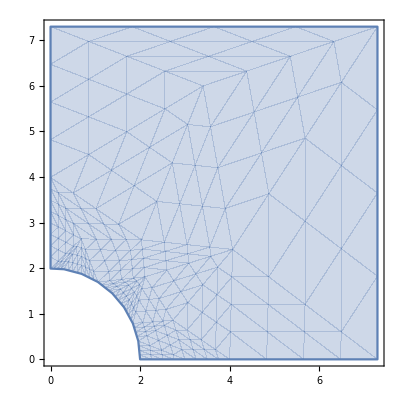

```mathematica
RegionPlot[region]
```

```mathematica
<<NDSolve`FEM`
```

```mathematica
mesh = ToElementMesh[region,MaxCellMeasure->0.001]
```

ElementMesh[{{0.,7.3},{0.,7.3}},{TriangleElement[<79083>]}]

```mathematica
Clear[z,r]
solc = NDSolveValue[
{lpc==NeumannValue[0,r==0&&a<z<b] + NeumannValue[0,z==0&&a<r<b],
DirichletCondition[ϕ[r,z]==-1,r^2+z^2==a^2],
ϕ[r,h/2]==0, ϕ[b,z]==0},ϕ, {r,z}∈mesh
]
```

InterpolatingFunction[{{0., 7.3}, {0., 7.3}}, <>]

```mathematica
solc["ElementMesh"]
```

ElementMesh[{{0.,7.3},{0.,7.3}},{TriangleElement[<79083>]}]

```mathematica
GetFromSolc[x_,z_]:=If[Sqrt[x^2+z^2]<=a,-1,solc[x,z]]
EstimateEField[x_,z_]:=Module[{step, Er,Ez},
step = 0.0005;
Er = -(GetFromSolc[Abs[x+step/2],Abs[z]]-GetFromSolc[Abs[x-step/2],Abs[z]])/step;
Ez = -(GetFromSolc[Abs[x],Abs[z+step/2]]-GetFromSolc[Abs[x],Abs[z-step/2]])/step;
{Er,Ez}
]
```

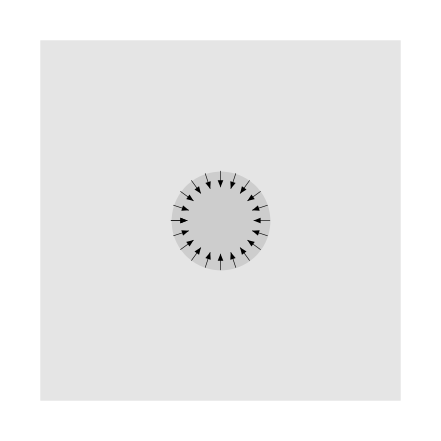

```mathematica
efieldvecs=Table[{{(a+gs) Cos[theta],(a+gs) Sin[theta]},{(a+gs) Cos[theta],(a+gs) Sin[theta]}+{-GetEField[1,(a+gs) Cos[theta],0,(a+gs) Sin[theta]][[1]],-GetEField[1,(a+gs) Cos[theta],0,(a+gs) Sin[theta]][[3]]}},{theta,-Pi,Pi, Pi/10}];Show[Graphics[{Thickness[0.001],Arrowheads[0.02],Arrow[efieldvecs]}],Graphics[{Opacity[0.1],Disk[{0,0},a],Rectangle[{-b,-h/2},{b,h/2}]}]]
```

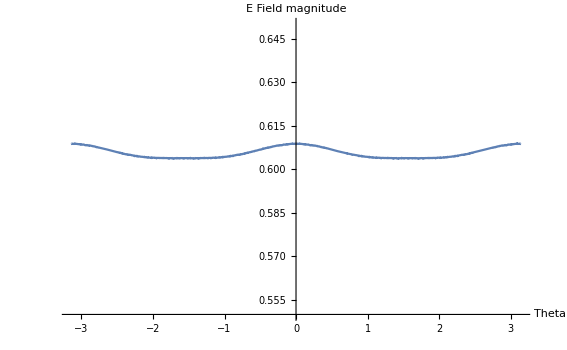

```mathematica
d=0.1;
Plot[Norm[EstimateEField[(a+d) Cos[theta],(a+d) Sin[theta]]],{theta,-Pi,Pi},PlotRange->{0.55,0.65},AxesLabel->{"Theta","E Field magnitude"}]
```

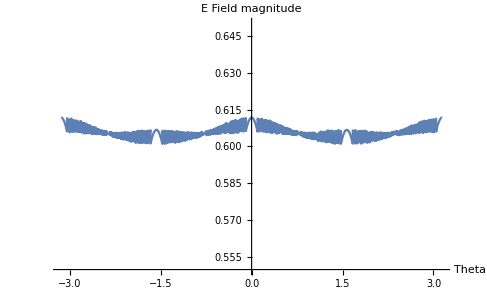

```mathematica
Plot[Norm[GetEField[1,(a+d) Cos[theta],0,(a+d) Sin[theta]]],{theta,-Pi,Pi},PlotRange->{0.55,.65},AxesLabel->{"Theta","E Field magnitude"}]
```

```mathematica
d=1;
errors=Table[(Norm[EstimateEField[(a+d) Cos[theta],(a+d) Sin[theta]]]-Norm[GetEField[1,(a+d) Cos[theta],0,(a+d) Sin[theta]]])/Norm[EstimateEField[(a+d) Cos[theta],(a+d) Sin[theta]]],{theta, -Pi,Pi,Pi/20000}];
100*Max[errors]
```

0.32659

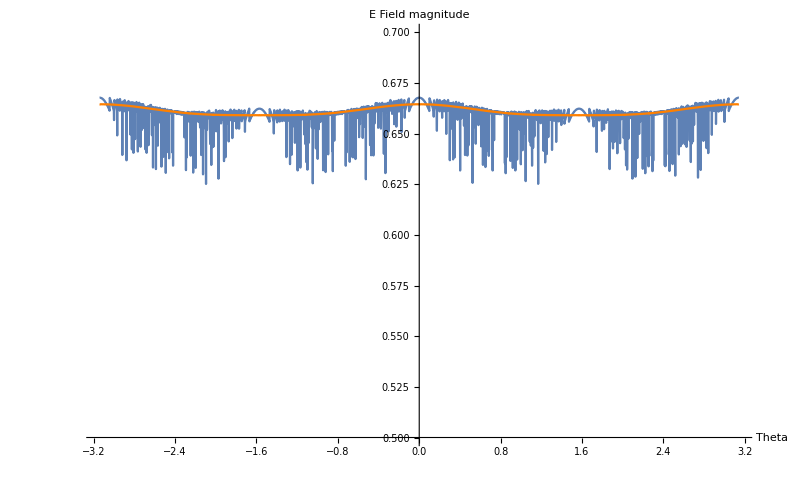

```mathematica
d=0.01;
Show[Plot[Norm[GetEField[1,(a+d) Cos[theta],0,(a+d) Sin[theta]]],{theta,-Pi,Pi},PlotRange->{0.5,0.7}], Plot[Norm[EstimateEField[(a+d) Cos[theta],(a+d) Sin[theta]]],{theta,-Pi,Pi},PlotStyle->Orange],AxesLabel->{"Theta","E Field magnitude"}]
```

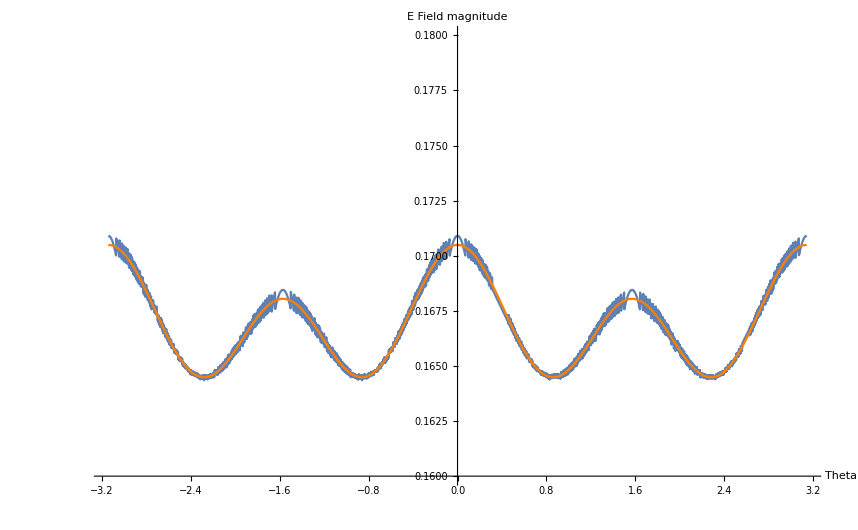

```mathematica
d=2;
Show[Plot[Norm[GetEField[1,(a+d) Cos[theta],0,(a+d) Sin[theta]]],{theta,-Pi,Pi},PlotRange->{0.16,0.18}], Plot[Norm[EstimateEField[(a+d) Cos[theta],(a+d) Sin[theta]]],{theta,-Pi,Pi},PlotStyle->Orange],AxesLabel->{"Theta","E Field magnitude"}]
```

1

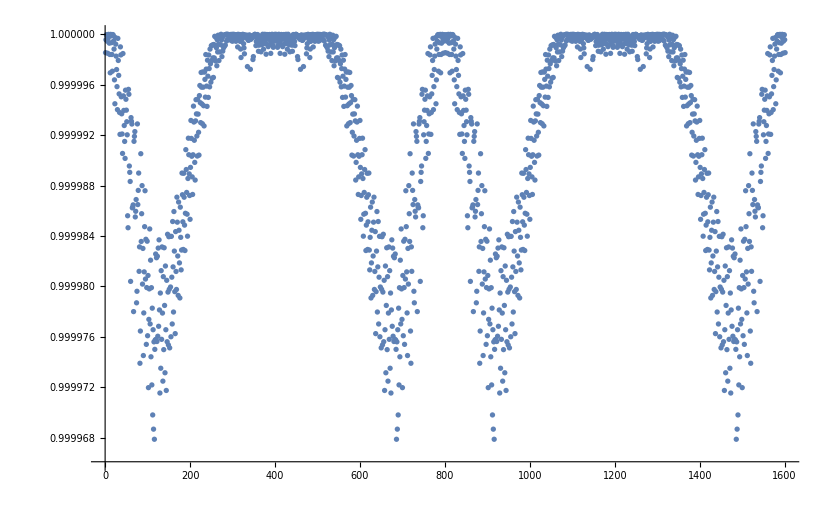

```mathematica
d=1
directions=Table[(GetEField[1,(a+d) Cos[theta],0,(a+d) Sin[theta]].{Cos[theta],0, Sin[theta]})/Norm[GetEField[1,(a+d) Cos[theta],0,(a+d) Sin[theta]]],{theta,-Pi,Pi,2Pi/1600}];
ListPlot[directions]
```

```mathematica
(*degrees of inaccuracy*)
ArcCos[Min[directions]]180/Pi
```

0.459241

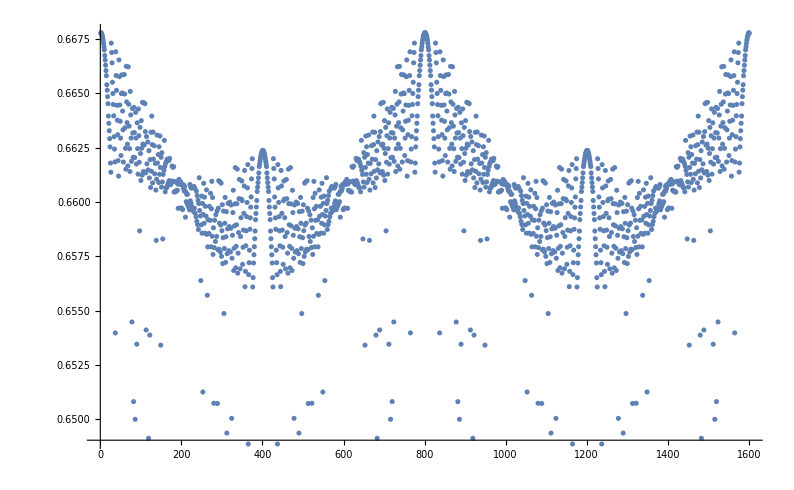

```mathematica
mags=Table[Norm[GetEField[1,(a+gs) Cos[theta],0,(a+gs) Sin[theta]]],{theta,-Pi,Pi,2Pi/1600}];
ListPlot[mags]
```

```mathematica
testPoints={{4.608842669337616,6.563585696985424},{3.707180200517526,2.176750103748627},{3.792037566239333,4.787781408276944},{3.855778982477084,6.2237642461949205},{0.5816942256367047,6.431626072609152},{1.866278784790517,1.5856972073106224},{2.905554076101517,0.3042719406065806},{4.575278216079155,4.368535882641796},{0.15228864787249807,6.7965613936293},{3.0835338797819465,1.126015266510481},{0.8357538179378818,4.235467354793811},{1.838948320701085,4.892962053921949},{0.6921786231648643,1.984597266088046},{1.6282948913230884,6.1271049030900615},{6.260241423248773,4.049899219509415},{4.314099980656643,6.682551100251801},{3.13939323464767,3.2866671843639033},{2.5535700266727304,6.458169956398989},{6.4600376108498825,2.845434570939234},{5.915655343265746,5.078591103153024}};
```

```mathematica
testResults = Table[
Module[{e1,e2,n1,n2,diff,cos},
e1=-{GetEField[1,point[[1]],0,point[[2]]][[1]], GetEField[1,point[[1]],0,point[[2]]][[3]]};
e2=EstimateEField[point[[1]],point[[2]]];
n1=Norm[e1];
n2=Norm[e2];
diff=2(n1-n2)/(n1+n2);
cos=e1.e2/(n1 n2);
{point,e1,e2, n1,n2,diff,cos }
], {point,testPoints}];
testResults=Insert[testResults,{"Point","E from File", "E from Laplace", "Norm 1", "Norm 2", "Difference", "Cos"},1];
Print[phiFile];
Grid[testResults,Frame->All,Spacings->2]
```

Phi file: 2/5/2023 Phi from 2D cylindrical solve

Point | E from File | E from Laplace | Norm 1 | Norm 2 | Difference | Cos
{4.60884,6.56359} | {-0.00958667,-0.0314003} | {-0.00958494,-0.0314021} | 0.0328311 | 0.0328324 | -0.0000379209 | 1.
{3.70718,2.17675} | {-0.125929,-0.0692497} | {-0.125842,-0.0692609} | 0.143714 | 0.143643 | 0.000492979 | 1.
{3.79204,4.78778} | {-0.0390244,-0.0523992} | {-0.0390244,-0.052376} | 0.0653344 | 0.0653158 | 0.00028492 | 1.
{3.85578,6.22376} | {-0.0145572,-0.0426574} | {-0.0145568,-0.0426622} | 0.0450728 | 0.0450773 | -0.0000997828 | 1.
{0.581694,6.43163} | {-0.0031235,-0.0775592} | {-0.00310674,-0.0775946} | 0.0776221 | 0.0776567 | -0.000446382 | 1.
{1.86628,1.5857} | {-0.339956,-0.287458} | {-0.339769,-0.287402} | 0.445199 | 0.44502 | 0.000403887 | 1.
{2.90555,0.304272} | {-0.313846,-0.0323101} | {-0.313743,-0.0322276} | 0.315505 | 0.315394 | 0.000350693 | 1.
{4.57528,4.36854} | {-0.0442936,-0.0390171} | {-0.0442909,-0.0390052} | 0.0590275 | 0.0590177 | 0.000166391 | 1.
{0.152289,6.79656} | {-0.000472751,-0.0755912} | {-0.000464495,-0.0755819} | 0.0755926 | 0.0755833 | 0.000123898 | 1.
{3.08353,1.12602} | {-0.234641,-0.083352} | {-0.234826,-0.0833882} | 0.249006 | 0.249192 | -0.000749257 | 1.
{0.835754,4.23547} | {-0.0265261,-0.142051} | {-0.0265446,-0.142025} | 0.144506 | 0.144484 | 0.000153714 | 1.
{1.83895,4.89296} | {-0.0306978,-0.0936121} | {-0.0307348,-0.0936649} | 0.0985169 | 0.0985786 | -0.000625871 | 1.
{0.692179,1.9846} | {-0.19912,-0.569007} | {-0.198592,-0.569215} | 0.602842 | 0.602863 | -0.0000362365 | 1.
{1.62829,6.1271} | {-0.010915,-0.0733952} | {-0.010932,-0.0733701} | 0.0742024 | 0.07418 | 0.000301489 | 1.
{6.26024,4.0499} | {-0.0388513,-0.0123728} | {-0.0388805,-0.0123718} | 0.0407739 | 0.0408013 | -0.000672549 | 1.
{4.3141,6.68255} | {-0.00811807,-0.0351415} | {-0.00811806,-0.0351454} | 0.036067 | 0.0360708 | -0.00010719 | 1.
{3.13939,3.28667} | {-0.0881766,-0.0900567} | {-0.0881195,-0.0900236} | 0.126037 | 0.125973 | 0.000505233 | 1.
{2.55357,6.45817} | {-0.0101184,-0.0595603} | {-0.0101166,-0.0595414} | 0.0604137 | 0.0603947 | 0.000314094 | 1.
{6.46004,2.84543} | {-0.0527552,-0.00926054} | {-0.0528024,-0.00926173} | 0.0535619 | 0.0536085 | -0.000870031 | 1.
{5.91566,5.07859} | {-0.0269175,-0.0162529} | {-0.0269149,-0.016249} | 0.0314437 | 0.0314395 | 0.000132705 | 1.

```mathematica
testResultsv2 = Table[{
point,
-GetPotential[1,point[[1]],0,point[[2]]],
solc[point[[1]],point[[2]]],
100*(solc[point[[1]],point[[2]]]+GetPotential[1,point[[1]],0,point[[2]]])/solc[point[[1]],point[[2]]]}//N,
{point,testPoints}];
testResultsv2=Insert[testResultsv2,{"Point","Potential from File", "Potential from Laplace","Percent Error"},1];
Grid[testResultsv2,Frame->All,Spacings->2]
```

Point | Potential from File | Potential from Laplace | Percent Error
{4.60884,6.56359} | -0.0228437 | -0.0228436 | -0.0000893453
{3.70718,2.17675} | -0.285638 | -0.285638 | -0.000119639
{3.79204,4.78778} | -0.113569 | -0.113568 | -0.0000966593
{3.85578,6.22376} | -0.0444733 | -0.0444733 | -0.0000920436
{0.581694,6.43163} | -0.0647829 | -0.0647828 | -0.0000635923
{1.86628,1.5857} | -0.755247 | -0.755245 | -0.000283062
{2.90555,0.304272} | -0.576356 | -0.576355 | -0.000247503
{4.57528,4.36854} | -0.0999098 | -0.0999097 | -0.000092579
{0.152289,6.79656} | -0.0375394 | -0.0375394 | -0.000113133
{3.08353,1.12602} | -0.476133 | -0.476132 | -0.000172861
{0.835754,4.23547} | -0.28458 | -0.284579 | -0.000140282
{1.83895,4.89296} | -0.177993 | -0.177992 | -0.000109267
{0.692179,1.9846} | -0.935483 | -0.935479 | -0.000463012
{1.62829,6.1271} | -0.0807665 | -0.0807664 | -0.000110662
{6.26024,4.0499} | -0.0374481 | -0.0374481 | -5.93771×10^-6
{4.3141,6.68255} | -0.0214964 | -0.0214964 | -0.0000969176
{3.13939,3.28667} | -0.256277 | -0.256277 | -0.0000666832
{2.55357,6.45817} | -0.0487486 | -0.0487486 | -0.0000427234
{6.46004,2.84543} | -0.0414332 | -0.0414332 | 0.0000257004
{5.91566,5.07859} | -0.0340119 | -0.0340119 | -0.000136803

```mathematica
points=Reap[AvgElectronsEulerSC[53/100,1,15,2/5,99/100,True,10]][[2]]
```

1000 * RMS travel error: 1.77026

V/NC 1.5

λ: 53/100

Geometry: SC

Collisions: 10.01.3

Mean path: 8.8186

```mathematica
Show[Graphics3D[ {Opacity[0.3],Cylinder[{{0,0,-7.3},{0,0,7.3}},7.3]}],Graphics3D[Ball[{0,0,0},2]],Graphics3D[{Black,PointSize[0.01],Point[points[[1]]]}]]
```

-Graphics3D-

### Sphere-in-cylinder MC’s

```mathematica
AvgElectronsEulerSC[λ_,Ni_,Ui_,dt_,tbound_,print_,getbins_,count_] := Module[{eErrorList,V,result,stack,collisions,paths,svals,countbin,electronsbin,squaredbin,lbin,lbinSquared,data, seedcount,totalpaths,Nc},
V=Ui*Ni;
totalpaths=0;
seedcount=1;
collisions={};
eErrorList={};
paths = {};
svals = 0;
If[getbins,
countbin = Table[0,2/binwidth];
electronsbin =  Table[0,2/binwidth];
squaredbin= Table[0,2/binwidth];
lbin = Table[0,lmax/2+1];
lbinSquared =  Table[0,lmax/2+1,lmax/2+1]];
data = {};
stack = CreateDataStructure["Stack"];
result = Table[
Module[{x0,x1,y0,y1,z0,z1,numElectrons,cosθ,ϕ,s,vx,vy,vz, energy,eError,numCollisions,pathval,sval,idx,cθ0,ϕ0,SH,l,l2,collisionE,cost,phi,start,path,input},
numElectrons = 1; 
numCollisions=0;
stack["Push",GetStartingPos[]];
{cθ0,ϕ0} = GetAngles[x0,y0,z0];
While[! stack["EmptyQ"],
{x0,y0,z0,vx,vy,vz}=stack["Pop"];
cosθ=1;
ϕ=0;
energy=0;
path=0;
While[
s=RandomVariate[ExponentialDistribution[1/λ],WorkingPrecision->16];
{x1,y1,z1, vx, vy, vz, energy,eError,pathval,sval}=GetNewPositionsEuler[dt,s,V,x0,y0,z0,vx,vy,vz];
AppendTo[eErrorList,eError];
InBounds[x1,y1,z1],
path+=pathval;
AppendTo[paths,pathval];
svals+=s;
numCollisions++;
If[energy>=Ui,
numElectrons++;
stack["Push",{x1,y1,z1,0,0,0}];
energy-=Ui,
collisionE=SetPrecision[Ui*RandomVariate[UniformDistribution[{1/10, 1/2}]],16];
energy-=collisionE;
If[energy<0,energy=0];
];
{vx, vy, vz, cost, phi}=UpdateVelocity[energy, vx, vy, vz, tbound];
{x0,y0,z0}={x1,y1,z1};
];
totalpaths+=path;
]; 
AppendTo[data,{cθ0,numElectrons}];
If[getbins,
idx=FindBinNum[cθ0,binwidth];
countbin[[idx]]+=1;
electronsbin[[idx]]+=numElectrons;
squaredbin[[idx]]+=numElectrons^2;
SH=numElectrons Table[Conjugate[SphericalHarmonicY[l,0,ArcCos[cθ0],ϕ0]],{l,0,lmax,2}];
For[l= 0, l <= lmax, l+=2,
lbin[[l/2+1]]+=SH[[l/2+1]];
For[l2=0,l2<=lmax,l2+=2,
lbinSquared[[l/2+1,l2/2+1]]+=SH[[l/2+1]]SH[[l2/2+1]]
]
];
];
AppendTo[collisions,numCollisions];
numElectrons],
{count}];
If[print,
Print["1000 * RMS travel error: ",1000*RootMeanSquare[eErrorList]];
Print["V/NC ",Ni Ui λ/5.3];
Print["λ: ",λ];
Print["Geometry: ",ID];
Print["Collisions: ", Around[Mean[collisions],StandardDeviation[collisions]/Sqrt[count]]];
Print["Mean path: ",  totalpaths/count/λ];
Print[phiFile]
];
Sow[data ];
Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

```mathematica
a={{5.0,2.0,3.0},{2.0,7.0,5.0},{3.0,5.0,6.0}};
Print[a//MatrixForm];
Print[CholeskyDecomposition[a]//MatrixForm];
Print[LinearSolve[a,{1,2,3}]];
```

(5. | 2. | 3.
2. | 7. | 5.
3. | 5. | 6.)

(2.23607 | 0.894427 | 1.34164
0. | 2.48998 | 1.52612
0. | 0. | 1.36783)

{-0.172414,-0.206897,0.758621}

### Creating a faster version to run in-parallel

```mathematica
AbsoluteTiming[AvgElectronsEulerSCFAST[1/2,10,15,2/5,4/5,True,False,400]]
```

1000 * RMS travel error: 14.7028

V/NC 14.1509

λ: 1/2

Geometry: SC

Collisions: 205.5.

Phi file: 2/5/2023 Phi from 2D cylindrical solve

{394.169,34.50.7}

```mathematica
MaxElectronsFAST[1/2,10,500]
```

-1.

39.5.

```mathematica
AvgElectronsEulerSCFAST[λ_,Ni_,Ui_,dt_,tbound_,print_,getbins_,count_] := Module[{masterdata,eErrorList,V,result,stack,collisions,paths,svals,eErrorListMASTER,countbin,electronsbin,squaredbin,lbin,lbinSquared, seedcount,totalpaths,Nc},
V=Ui*Ni;
seedcount=1;
collisions={};
(*each kernel creates its own version of eErrorList*)
eErrorListMASTER={};
paths = {};
svals = 0;
If[getbins,
countbin = Table[0,2/binwidth];
electronsbin =  Table[0,2/binwidth];
squaredbin= Table[0,2/binwidth];
lbin = Table[0,lmax/2+1];
lbinSquared =  Table[0,lmax/2+1,lmax/2+1]];
masterdata = {};
result = ParallelTable[
Module[{x0,x1,y0,y1,z0,z1,numElectrons,cosθ,ϕ,s,vx,vy,vz, energy,data,eError,numCollisions,pathval,sval,idx,cθ0,ϕ0,SH,l,l2,collisionE,cost,phi,start,path,input},
numElectrons = 1; 
numCollisions=0;
eErrorList={};
stack = CreateDataStructure["Stack"];
stack["Push",GetStartingPos[]];
{cθ0,ϕ0} = GetAngles[x0,y0,z0];
While[!stack["EmptyQ"],
{x0,y0,z0,vx,vy,vz}=stack["Pop"];
cosθ=1;
ϕ=0;
energy=0;
data = {};
path=0;
While[
s=RandomVariate[ExponentialDistribution[1/λ],WorkingPrecision->16];
{x1,y1,z1, vx, vy, vz, energy,eError,pathval,sval}=GetNewPositionsEuler[dt,s,V,x0,y0,z0,vx,vy,vz];
AppendTo[eErrorList,eError];
InBounds[x1,y1,z1],
path+=pathval;
AppendTo[paths,pathval];
svals+=s;
numCollisions++;
If[energy>=Ui,
numElectrons++;
stack["Push",{x1,y1,z1,0,0,0}];
energy-=Ui,
collisionE=SetPrecision[Ui*RandomVariate[UniformDistribution[{1/10, 1/2}]],16];
energy-=collisionE;
If[energy<0,energy=0];
];
{vx, vy, vz, cost, phi}=UpdateVelocity[energy, vx, vy, vz, tbound];
{x0,y0,z0}={x1,y1,z1};
];
]; 
AppendTo[data,{cθ0,numElectrons}];
If[getbins,
idx=FindBinNum[cθ0,binwidth];
countbin[[idx]]+=1;
electronsbin[[idx]]+=numElectrons;
squaredbin[[idx]]+=numElectrons^2;
SH=numElectrons Table[Conjugate[SphericalHarmonicY[l,0,ArcCos[cθ0],ϕ0]],{l,0,lmax,2}];
For[l= 0, l <= lmax, l+=2,
lbin[[l/2+1]]+=SH[[l/2+1]];
For[l2=0,l2<=lmax,l2+=2,
lbinSquared[[l/2+1,l2/2+1]]+=SH[[l/2+1]]SH[[l2/2+1]]
]
];
];
{numElectrons, eErrorList, numCollisions, Last[data]}],
{count}];
collisions=Flatten[#[[3]]&/@result];
eErrorListMASTER=Flatten[#[[2]]&/@result];
masterdata=#[[4]]&/@result;
result=Flatten[#[[1]]&/@result];
If[print,
Print["1000 * RMS travel error: ",1000*RootMeanSquare[Flatten[eErrorListMASTER]]];
Print["V/NC ",Ni Ui λ/5.3];
Print["λ: ",λ];
Print["Geometry: ",ID];
Print["Collisions: ", Around[Mean[collisions],StandardDeviation[collisions]/Sqrt[count]]];
Print[phiFile]
];
Sow[masterdata];
Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

### Playing with spherical harmonics (using standardized testing data)

```mathematica
Import["/Users/wbowers/Downloads/testData1.txt", "Table"]
```

{{Command,line:,emc,Ni=11.3,Nc=10,Ui=15,reps=10000,dt=1e-3,scatter=0.8,seed=1,shape=scf,phifile=cwPhi.txt,showpath=true,pathnum=-2},{},{-0.24765,121},{0.58485,30},{0.82089,64},{0.51459,60},{0.53806,47},{-0.75322,74},{-0.39226,42},{-0.80142,69},{0.51232,13},{-0.17224,62},{-0.15049,37},{-0.57335,67},{0.66387,29},{0.95469,35},{0.29807,100},9968,{0.25002,37},{-0.98531,44},{-0.48698,34},{0.99284,27},{0.27253,84},{-0.37638,49},{0.43035,20},{-0.37275,37},{-0.36154,33},{-0.33106,32},{0.40546,16},{0.35234,68},{-0.67814,12},{0.12916,37},{-0.18555,14},{-0.93947,85},{0.26674,68}}
 |  |  |  |

```mathematica
SHtestdata=Drop[Import["/Users/wbowers/Downloads/testData1", "Table"],2];
(*SHtestdata2=Drop[Import["/Users/wbowers/Downloads/testData2.txt", "Table"],2];*)
```

```mathematica
SHtestdata
```

{{-0.24765,121},{0.58485,30},{0.82089,64},{0.51459,60},{0.53806,47},{-0.75322,74},{-0.39226,42},{-0.80142,69},{0.51232,13},{-0.17224,62},{-0.15049,37},{-0.57335,67},{0.66387,29},{0.95469,35},{0.29807,100},{0.96864,28},{-0.25395,82},{-0.51817,52},{-0.99356,69},{-0.32185,43},{-0.39371,27},{0.55179,24},9957,{-0.70103,51},{-0.33805,14},{0.67886,29},{0.61775,31},{0.25002,37},{-0.98531,44},{-0.48698,34},{0.99284,27},{0.27253,84},{-0.37638,49},{0.43035,20},{-0.37275,37},{-0.36154,33},{-0.33106,32},{0.40546,16},{0.35234,68},{-0.67814,12},{0.12916,37},{-0.18555,14},{-0.93947,85},{0.26674,68}}
 |  |  |  |

```mathematica
MakeElectronsPlot[data_]:=Module[{tenthOrderFit,SHYs,max,error,res,electrons,electronsSquared,counts,finalbins,half,temp,symbins,symcounts,symsquaredbins,errors,finalsymbins,cθ0,numelectrons},
tenthOrderFit=LinearModelFit[data,Table[SphericalHarmonicY[l,0,t,0],{l,0,10,2}]/.Cos[t]->z,z,IncludeConstantBasis->False];
SHYs=Table[SphericalHarmonicY[l,0,t,0],{l,0,lmax,2}]/.{Cos[t]->z};
max=NMaximize[{tenthOrderFit[z],-1<=z<=1},z];
error = Sqrt[SHYs.tenthOrderFit["CovarianceMatrix"].Transpose[SHYs]]/.max[[2]];
res=Around[max[[1]],error];
electrons=Table[0,2/binwidth];
electronsSquared=Table[0,2/binwidth];
counts = Table[0,2/binwidth];
For[i=1,i<=Length[data],i++,
{cθ0,numelectrons}=data[[i]];
idx=FindBinNum[cθ0,binwidth];
electrons[[idx]]+=numelectrons;
electronsSquared[[idx]]+=numelectrons^2;
counts[[idx]]+=1
];
finalbins=electrons/counts;
finalbins=Transpose[{Table[theta,{theta,-0.975,0.975,binwidth}],finalbins}];

half=Length[finalbins]/2;
temp=#[[2]]&/@finalbins;

symbins=(temp[[1;;half]]+Reverse[temp[[half+1;;Length[temp]]]])/2;
symcounts=(counts[[1;;half]]+Reverse[counts[[half+1;;Length[counts]]]])/2;
symsquaredbins=(electronsSquared[[1;;half]]+Reverse[electronsSquared[[half+1;;Length[electronsSquared]]]])/2;

symbins =Flatten[AppendTo[symbins,Reverse[symbins]]];
symcounts=Flatten[AppendTo[symcounts,Reverse[symcounts]]];
symsquaredbins =Flatten[AppendTo[symsquaredbins,Reverse[symsquaredbins]]];

symbins=Transpose[{Table[theta,{theta,-0.975,0.975,binwidth}],symbins}];
symsquaredbins=Transpose[{Table[theta,{theta,-0.975,0.975,binwidth}],symsquaredbins}];

errors =Sqrt[(#[[2]]&/@symsquaredbins)/symcounts -(#[[2]]&/@symbins)^2]/Sqrt[symcounts];
finalsymbins=symbins;

Print[finalbins];

For[i=1,i<=Length[errors],i++,finalsymbins[[i]] = {symbins[[i,1]],Around[symbins[[i,2]],errors[[i]]]}];
Show[ListPlot[finalsymbins,PlotLegends->{"symmetrized cos(theta) bins"}],Plot[tenthOrderFit[x],{x,-1,1},PlotStyle->Orange,PlotLegends->{"spherical harmonics fit (lmax = 10)"}],Graphics[{Red,Thickness[0.008],Circle[{z/.max[[2]],max[[1]]},{0.05,1.1}]}],Graphics[{Text[ToString[Round[res[[1]],0.1]] <> " ± " <> ToString[Round[res[[2]],0.01]]<> " electrons",{(z/.max[[2]] )+0.25,55}],Text["θ = "<>ToString[ArcCos[(z/.max[[2]])]*1/Degree]<>"°",{(z/.max[[2]] )+0.25,43}]}],Graphics[{Dashed,Black,Line[{{z/.max[[2]],20},{z/.max[[2]],max[[1]]}}]}],AxesOrigin->{0,30},PlotRange->{30,60},AxesLabel->{"cos(θ)","electrons"}]
]
```

{{-0.975,13213/251},{-0.925,12707/249},{-0.875,13771/270},{-0.825,13102/257},{-0.775,5949/124},{-0.725,11422/243},{-0.675,11583/226},{-0.625,6272/137},{-0.575,13790/269},{-0.525,7031/143},{-0.475,13244/251},{-0.425,667/13},{-0.375,12921/253},{-0.325,12401/240},{-0.275,1807/35},{-0.225,12193/244},{-0.175,417/8},{-0.125,4049/79},{-0.075,12774/241},{-0.025,12330/253},{0.025,6851/134},{0.075,11982/233},{0.125,6197/127},{0.175,12313/240},{0.225,15179/276},{0.275,3275/67},{0.325,11923/243},{0.375,11893/247},{0.425,6464/125},{0.475,5273/114},{0.525,4207/83},{0.575,11851/243},{0.625,13570/263},{0.675,12372/259},{0.725,11673/236},{0.775,12621/244},{0.825,11744/237},{0.875,12879/247},{0.925,10726/219},{0.975,1391/27}}

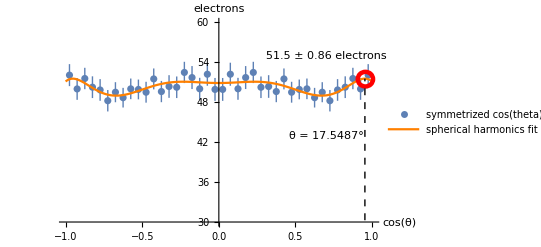

```mathematica
fig6=MakeElectronsPlot[SHtestdata2]
```

```mathematica
Export["/Users/wbowers/Documents/stem-fellowship/tif-figs/sh-fitting.TIFF",fig6,ImageResolution->600]
```

/Users/wbowers/Documents/stem-fellowship/tif-figs/sh-fitting.TIFF

{{-0.975,10810/221},{-0.925,12867/248},{-0.875,1147/23},{-0.825,643/13},{-0.775,13124/263},{-0.725,14281/276},{-0.675,13084/267},{-0.625,12571/253},{-0.575,13422/265},{-0.525,11911/240},{-0.475,14579/274},{-0.425,2174/41},{-0.375,13676/265},{-0.325,13487/250},{-0.275,6620/129},{-0.225,11719/229},{-0.175,2887/57},{-0.125,13519/271},{-0.075,14601/278},{-0.025,3774/73},{0.025,7103/136},{0.075,12707/257},{0.125,13036/259},{0.175,566/11},{0.225,14013/274},{0.275,6796/139},{0.325,12381/248},{0.375,5893/117},{0.425,3833/75},{0.475,11667/229},{0.525,11419/225},{0.575,11437/237},{0.625,1255/26},{0.675,11627/233},{0.725,1901/40},{0.775,234/5},{0.825,12908/261},{0.875,12053/227},{0.925,6614/125},{0.975,12419/237}}

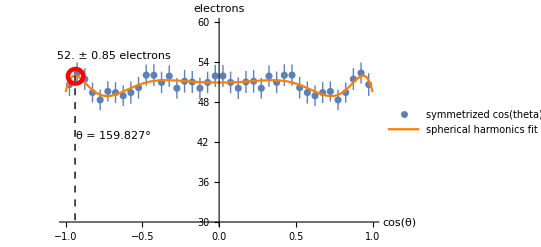

```mathematica
MakeElectronsPlot[SHtestdata]
```

```mathematica
r=Reap[AvgElectronsEulerSCFAST[53/34,40,15,2/5,4/5,True,False,50000]]
```

1000 * RMS travel error: 149.96

V/NC 176.471

λ: 53/34

Geometry: SC

Collisions: 42.470.20

Phi file: 2/5/2023 Phi from 2D cylindrical solve

{32.920.15,{{{{0.360795,71},{0.598697,88},{-0.974832,38},{-0.767807,18},{-0.489686,17},{0.7662,20},{0.151377,6},{0.417244,12},{-0.205477,45},{-0.0468744,14},{-0.109721,19},{-0.530765,50},49977,{0.275548,17},{0.411143,40},{0.138401,5},{0.791972,11},{-0.960341,7},{0.774839,4},{0.908373,22},{0.861046,62},{-0.448823,5},{-0.865586,27},{-0.119944,21}}}}}
 |  |  |  |

{{-0.975,103/4},{-0.925,42773/1344},{-0.875,15397/421},{-0.825,51929/1243},{-0.775,3556/75},{-0.725,49355/1018},{-0.675,8771/178},{-0.625,25888/583},{-0.575,49362/1237},{-0.525,25157/652},{-0.475,44791/1250},{-0.425,43137/1366},{-0.375,41359/1373},{-0.325,36101/1330},{-0.275,17747/670},{-0.225,10755/443},{-0.175,16970/683},{-0.125,4624/193},{-0.075,30052/1285},{-0.025,4984/213},{0.025,29181/1286},{0.075,28301/1213},{0.125,16602/673},{0.175,32179/1338},{0.225,34483/1337},{0.275,11339/431},{0.325,34946/1329},{0.375,39847/1375},{0.425,10718/321},{0.475,44224/1243},{0.525,46561/1269},{0.575,16627/409},{0.625,17034/389},{0.675,45491/978},{0.725,3323/67},{0.775,15707/349},{0.825,24671/583},{0.875,7651/218},{0.925,20167/653},{0.975,11404/439}}

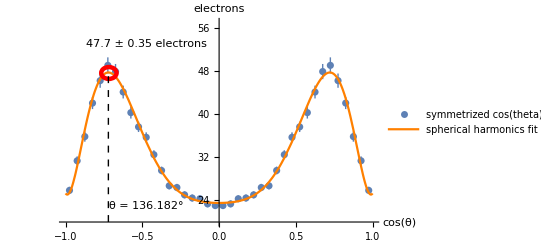

```mathematica
MakeElectronsPlot[r[[2,1,1]]]
```

```mathematica
p1=-Graphics-
```

-Graphics-

```mathematica
r2=Reap[AvgElectronsEulerSCFAST[53/700,171/10,15,2/5,4/5,True,False,5000]]
```

1000 * RMS travel error: 21.1145

V/NC 3.66429

λ: 53/700

Geometry: SC

Collisions: 2832.14.

Phi file: 2/5/2023 Phi from 2D cylindrical solve

{45.120.21,{{{{0.338099,90},{-0.962644,19},{-0.234118,49},{-0.608771,79},{-0.302092,61},{0.428077,38},{-0.63474,21},{-0.786352,26},{-0.811839,34},{0.378535,49},{0.752824,27},{-0.944244,20},4977,{-0.464546,19},{0.5626,39},{-0.0596975,40},{-0.438202,33},{-0.0369359,67},{0.045922,79},{0.339389,71},{-0.572022,35},{-0.210192,58},{-0.157178,32},{-0.0474263,36}}}}}
 |  |  |  |

{{-0.975,897/20},{-0.925,2174/49},{-0.875,1171/28},{-0.825,4852/113},{-0.775,3752/81},{-0.725,1351/30},{-0.675,1840/43},{-0.625,2844/65},{-0.575,2237/51},{-0.525,1519/36},{-0.475,5539/124},{-0.425,6149/137},{-0.375,7432/163},{-0.325,6892/149},{-0.275,7209/155},{-0.225,6992/147},{-0.175,6577/143},{-0.125,7638/163},{-0.075,8171/176},{-0.025,3597/73},{0.025,6957/145},{0.075,7655/159},{0.125,7403/167},{0.175,7251/154},{0.225,781/17},{0.275,3033/65},{0.325,6997/148},{0.375,3179/70},{0.425,6229/142},{0.475,1832/41},{0.525,1174/27},{0.575,5378/123},{0.625,3805/86},{0.675,1644/37},{0.725,983/23},{0.775,3028/77},{0.825,131/3},{0.875,6607/155},{0.925,6525/148},{0.975,6318/149}}

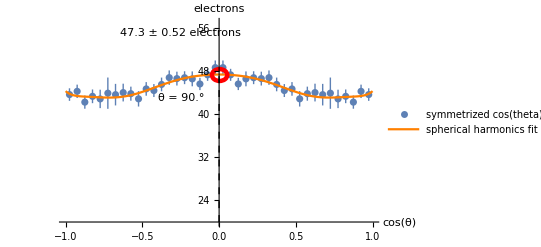

```mathematica
MakeElectronsPlot[r2[[2,1,1]]]
```

```mathematica
p2=-Graphics-
```

-Graphics-

```mathematica
Export["/Users/wbowers/Documents/stem-fellowship/tif-figs/e-bins-1.TIFF",p1,ImageResolution->600]
Export["/Users/wbowers/Documents/stem-fellowship/tif-figs/e-bins-2.TIFF",p2,ImageResolution->600]
```

/Users/wbowers/Documents/stem-fellowship/tif-figs/e-bins-1.TIFF

/Users/wbowers/Documents/stem-fellowship/tif-figs/e-bins-2.TIFF

### Using Spherical Harmonics to create max electrons function for sphere-in-cylinder

```mathematica
MaxElectrons[λ_,Ni_,reps_]:= Module[{idx,list,i,thetaslist,constants,SHYs,fit,max,error},
list =Last[Last[Reap[AvgElectronsEulerSC[λ,Ni,15,2/5,4/5,False,True,reps] ]]][[1]];
fit=LinearModelFit[list,Table[SphericalHarmonicY[l,0,theta,0],{l,0,lmax,2}]/.Cos[theta]->z,z,IncludeConstantBasis->False];
max=NMaximize[{fit[z],-1<=z<=1},z];
Print[z/.max[[2]]];
SHYs=Table[SphericalHarmonicY[l,0,theta,0],{l,0,lmax,2}]/.Cos[theta]->z;
error = Sqrt[SHYs.fit["CovarianceMatrix"].Transpose[SHYs]]/.max[[2]];
Around[max[[1]],error]
]
```

```mathematica
MaxElectronsFAST[λ_,Ni_,reps_]:= Module[{idx,list,i,thetaslist,constants,SHYs,fit,max,error},
list =Last[Last[Reap[AvgElectronsEulerSCFAST[λ,Ni,15,2/5,4/5,False,True,reps] ]]][[1]];
Clear[theta, z];
fit=LinearModelFit[list,Table[SphericalHarmonicY[l,0,theta,0],{l,0,lmax,2}]/.Cos[theta]->z,z,IncludeConstantBasis->False];
max=NMaximize[{fit[z],-1<=z<=1},z];
Print[z/.max[[2]]];
SHYs=Table[SphericalHarmonicY[l,0,theta,0],{l,0,lmax,2}]/.Cos[theta]->z;
error = Sqrt[SHYs.fit["CovarianceMatrix"].Transpose[SHYs]]/.max[[2]];
Around[max[[1]],error]
]
```

```mathematica
MaxElectronsFAST[53/100,12.1,500]
```

1.97348×10^-32

70.4.

```mathematica
MaxElectronsFAST[53/100,12.1,500]
```

1.03398×10^-25

69.4.

### Ensuring exponential growth of ions for the parallel plate case (1D AND 3D)

```mathematica
t1=Table[{Nc,AvgElectronsWeighted[Nc,Nc,1000] },{Nc,0.2,14,0.8}]
```

{{0.2,1},{1.,1},{1.8,1.2560.014},{2.6,1.6120.018},{3.4,2.0060.029},{4.2,2.550.04},{5.,3.170.06},{5.8,3.890.07},{6.6,4.890.10},{7.4,6.000.13},{8.2,7.960.17},{9.,9.470.22},{9.8,12.350.32},{10.6,14.90.4},{11.4,19.70.5},{12.2,23.30.6},{13.,28.90.9},{13.8,36.81.1}}

```mathematica
java1d={{0.2,Around[1.0,0.0]},{1.0,Around[1.0,0.0]},{1.8,Around[1.292,0.0]},{2.6,Around[1.6152,0.0]},{3.4000000000000004,Around[2.0128,0.0]},{4.2,Around[2.5308,0.0]},{5.0,Around[3.1744,0.0]},{5.8,Around[3.96,0.0]},{6.6,Around[4.8992,0.0]},{7.3999999999999995,Around[6.146,0.0]},{8.2,Around[7.778,0.0]},{9.0,Around[9.6872,0.0]},{9.8,Around[11.818,0.0]},{10.600000000000001,Around[14.9372,0.0]},{11.400000000000002,Around[18.5404,0.0]},{12.200000000000003,Around[22.9588,0.0]},{13.000000000000004,Around[29.3304,0.0]},{13.800000000000004,Around[36.6168,0.0]},{14.600000000000005,Around[45.6408,0.0]}}
```

{{0.2,1.},{1.,1.},{1.8,1.292},{2.6,1.6152},{3.4,2.0128},{4.2,2.5308},{5.,3.1744},{5.8,3.96},{6.6,4.8992},{7.4,6.146},{8.2,7.778},{9.,9.6872},{9.8,11.818},{10.6,14.9372},{11.4,18.5404},{12.2,22.9588},{13.,29.3304},{13.8,36.6168},{14.6,45.6408}}

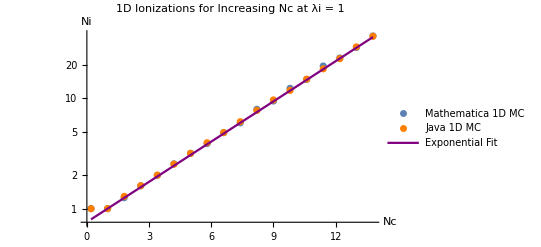

```mathematica
Show[ListLogPlot[t1,PlotLegends->{"Mathematica 1D MC"}],ListLogPlot[java1d,PlotStyle->Orange,PlotLegends->{"Java 1D MC"}],LogPlot[Exp[0.28(x-1)],{x,0.2,13.8},PlotStyle->Purple,PlotLegends->{"Exponential Fit"}],PlotLabel->"1D Ionizations for Increasing Nc at λi = 1",AxesLabel->{Nc,Ni}]
```

```mathematica
t2=Table[{Nc,AvgElectrons3D[Nc,Nc,5,15,0.8,100]},{Nc,0.2,14,0.8}]
```

{{0.2,1},{1.,1},{1.8,1.360.05},{2.6,1.880.07},{3.4,2.540.10},{4.2,3.410.14},{5.,5.310.20},{5.8,6.940.29},{6.6,10.150.35},{7.4,13.90.5},{8.2,20.60.7},{9.,26.21.0},{9.8,36.71.1},{10.6,51.31.7},{11.4,74.42.6},{12.2,102.13.3},{13.,136.5.},{13.8,195.7.}}

```mathematica
java3d={{0.2,Around[1.0,0.0]},{1.0,Around[1.0,0.0]},{1.8,Around[1.3708,0.009660380116744999]},{2.6,Around[1.8896,0.014252183552003757]},{3.4000000000000004,Around[2.6092,0.01951076994892846]},{4.2,Around[3.622,0.02711690247797481]},{5.0,Around[5.0172,0.03788458346082171]},{5.8,Around[7.038,0.05230891319842165]},{6.6,Around[9.6412,0.071414459488258]},{7.3999999999999995,Around[13.5272,0.0970370241918007]},{8.2,Around[18.8308,0.13820415530656086]},{9.0,Around[26.5088,0.18488258172148112]},{9.8,Around[36.892,0.25806691845333396]},{10.600000000000001,Around[51.484,0.353070726059242]},{11.400000000000002,Around[71.3404,0.49144933730344953]},{12.200000000000003,Around[98.8472,0.6953129517447517]},{13.000000000000004,Around[139.1028,0.961511358676537]},{13.800000000000004,Around[194.0804,1.3399496611201482]}}
```

{{0.2,1.},{1.,1.},{1.8,1.3710.010},{2.6,1.8900.014},{3.4,2.6090.020},{4.2,3.6220.027},{5.,5.020.04},{5.8,7.040.05},{6.6,9.640.07},{7.4,13.530.10},{8.2,18.830.14},{9.,26.510.18},{9.8,36.890.26},{10.6,51.480.35},{11.4,71.30.5},{12.2,98.80.7},{13.,139.11.0},{13.8,194.11.3}}

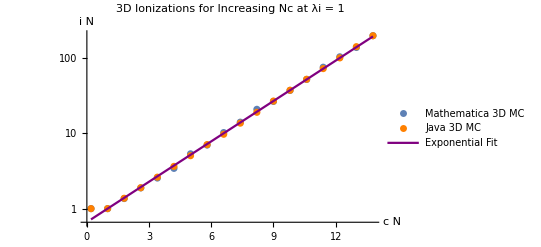

```mathematica
Show[ListLogPlot[t2,PlotLegends->{"Mathematica 3D MC"}],ListLogPlot[java3d,PlotStyle->Orange,PlotLegends->{"Java 3D MC"}],LogPlot[Exp[0.41(x-1)],{x,0.2,13.8},PlotStyle->Purple,PlotLegends->{"Exponential Fit"}],PlotLabel->"3D Ionizations for Increasing Nc at λi = 1",AxesLabel->{Nc,Ni}]
```

### Exploring 1D alphas

```mathematica
FindAlpha[λi_,reps_] := Module[{electrons,result,length,i,total,slopes,alpha,e,fittedmodel,a,b,c,d,params},
electrons = Table[{Nc,Log[AvgElectronsWeighted[Nc,((1/λi) Nc),reps]]},{Nc,λi+5,40,4}];
fittedmodel=NonlinearModelFit[{#[[1]],#[[2,1]]}&/@electrons,a*x + b + c Exp[-d x],{a,b,c,d},x];
params=fittedmodel["ParameterTable"][[1,1]];
{Around[params[[2,2]],params[[2,3]]],Around[params[[3,2]],params[[3,3]]]}]
```

```mathematica
markovmodel[x_]:= 1/x*ProductLog[x Exp[-x]]
```

```mathematica
javaalphas={{0.25,Around[0.6602595438326849,0.001904193660625115]},{0.5,Around[0.47844948673235005,0.001748144153630099]},{0.75,Around[0.35821274297950323,0.0031233087246661244]},{1.0,Around[0.27433365451618424,0.008691189348246631]},{1.25,Around[0.21314895885656557,0.013389317555812227]},{1.5,Around[0.1669038047699682,0.01749867647681158]},{1.75,Around[0.13018046550569878,0.014267346022973922]},{2.0,Around[0.1015082557377325,0.012894206875325626]},{2.2500000000000004,Around[0.078742597634773,0.011952013460590393]},{2.5,Around[0.061520625296323746,0.010962062286845231]},{2.75,Around[0.04725434577446056,0.00734274289001424]},{3.0,Around[0.0358071249036958,0.004959892432166247]},{3.25,Around[0.02778741774482209,0.004504199943380026]},{3.5,Around[0.021572007247372436,0.003796229153906858]},{3.7500000000000004,Around[0.015726014436025514,0.0022654561964774527]},{4.0,Around[0.012178682642516597,0.0017503399885901638]},{4.25,Around[0.008830658060106817,0.0010123646555449694]}}
```

{{0.25,0.66030.0019},{0.5,0.47840.0017},{0.75,0.35820.0031},{1.,0.2740.009},{1.25,0.2130.013},{1.5,0.1670.017},{1.75,0.1300.014},{2.,0.1020.013},{2.25,0.0790.012},{2.5,0.0620.011},{2.75,0.0470.007},{3.,0.0360.005},{3.25,0.0280.005},{3.5,0.0220.004},{3.75,0.01570.0023},{4.,0.01220.0018},{4.25,0.00880.0010}}

```mathematica
alphas1d=Table[{r,FindAlpha[r,1000][[1]]},{r,0.25,4.25,0.5}]
```

{{0.25,0.6390.010},{0.75,0.35630.0028},{1.25,0.21790.0022},{1.75,0.13820.0009},{2.25,0.08680.0009},{2.75,0.05290.0011},{3.25,0.03560.0018},{3.75,0.02120.0006},{4.25,0.01290.0006}}

```mathematica
alphas1d={{0.25,0.6390.010},{0.75,0.35630.0028},{1.25,0.21790.0022},{1.75,0.13820.0009},{2.25,0.08680.0009},{2.75,0.05290.0011},{3.25,0.03560.0018},{3.75,0.02120.0006},{4.25,0.01290.0006}}
```

{{0.25,0.6390.010},{0.75,0.35630.0028},{1.25,0.21790.0022},{1.75,0.13820.0009},{2.25,0.08680.0009},{2.75,0.05290.0011},{3.25,0.03560.0018},{3.75,0.02120.0006},{4.25,0.01290.0006}}

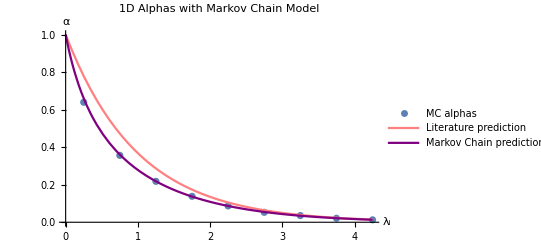

```mathematica
fig8=Show[ListPlot[alphas1d,PlotLegends->{"MC alphas"}],Plot[Exp[-x],{x,0,4.25},PlotLegends->{"Literature prediction"},PlotStyle->Pink],Plot[1/x*ProductLog[x Exp[-x]],{x,0,4.25},PlotStyle->Purple,PlotLegends->{"Markov Chain prediction"}],PlotRange->{0,1},AxesLabel->{Subscript["λ","i"],"α"},PlotLabel->"1D Alphas with Markov Chain Model"]
```

```mathematica
Export["/Users/wbowers/Documents/stem-fellowship/figures/alphas-plot-wb-version.TIFF",fig8,ImageResolution->600]
```

/Users/wbowers/Documents/stem-fellowship/figures/alphas-plot-wb-version.TIFF

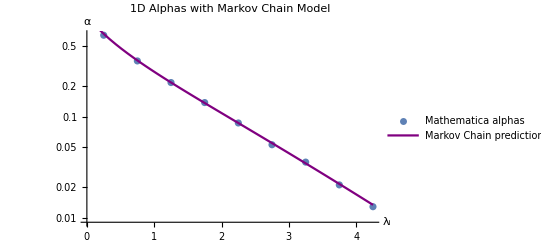

```mathematica
Show[ListLogPlot[alphas1d,PlotLegends->{"Mathematica alphas"}],LogPlot[1/x*ProductLog[x Exp[-x]],{x,0,4.25},PlotStyle->Purple,PlotLegends->{"Markov Chain prediction"}],AxesLabel->{Subscript["λ","i"],"α"},PlotLabel->"1D Alphas with Markov Chain Model"]
```

```mathematica
l1 = Reap[AvgElectrons3D[10,10,5000]]; l1[[1]]
```

39.790.19

### Examining the sample space for the alpha calculation

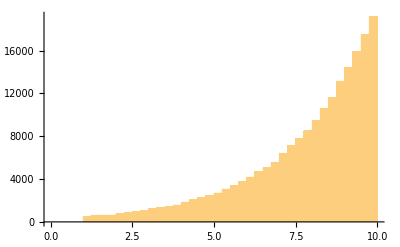

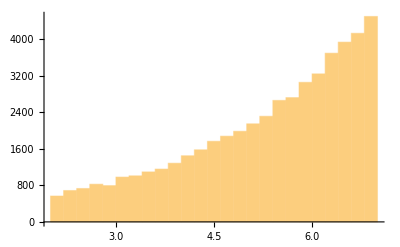

```mathematica
Histogram[l1[[2,1]],{0,10,0.25}]
Histogram[l1[[2,1]],{2,7,0.2}]
```

```mathematica
Clear[α]
FindAlphav2[λi_,x_]:= (Exp[-λi] - Exp[-x])/(1-Exp[-x])
Plot3D[FindAlphav2[λi,x],{λi,1/2,4},{x,1/2,5},AxesLabel->{λi,x,α}]
```

-Graphics3D-

```mathematica
FindRoot[FindAlphav2[1/2,x]==FindAlpha[1/2][[1]],{x,1,6}]
FindRoot[FindAlphav2[1,x]==FindAlpha[1][[1]],{x,1,6}]
FindRoot[FindAlphav2[4,x]==FindAlpha[4][[1]],{x,1,6}]
```

{x→1.42628}

{x→2.16402}

{x→6.78437}

12.650.06

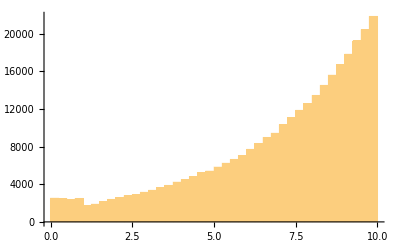

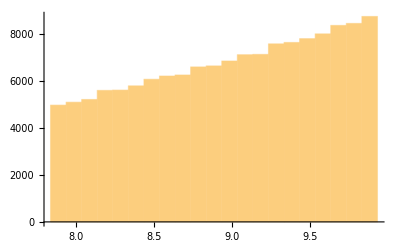

```mathematica
l1 = Reap[AvgElectronsBanked[10,10,10000]]; l1[[1]]
Histogram[l1[[2,1]],{0,10,0.25}]
Histogram[l1[[2,1]],{(10-2.16401),10,0.1}]
```

7.250.04

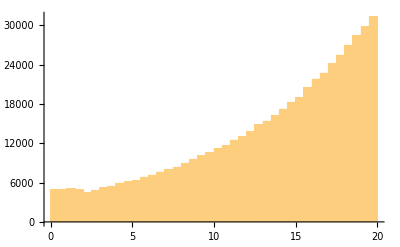

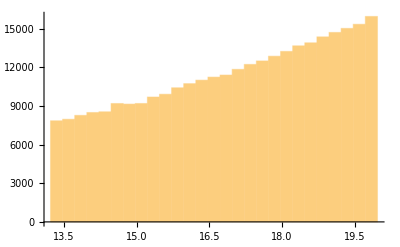

```mathematica
l2= Reap[AvgElectronsBanked[20,10,10000]]; l2[[1]]
Histogram[l2[[2,1]],{0,20,0.5}]
Histogram[l2[[2,1]],{20-6.78,20,0.25}]
```

95.40.5

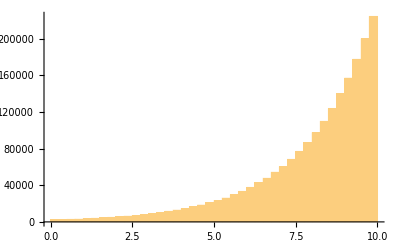

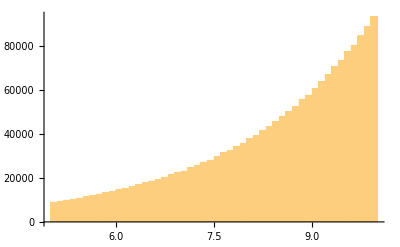

```mathematica
l3 = Reap[AvgElectronsBanked[10,20,10000]]; l3[[1]]
Histogram[l3[[2,1]],{0,10,0.25}]
Histogram[l3[[2,1]],{10-5,10,0.1}]
```

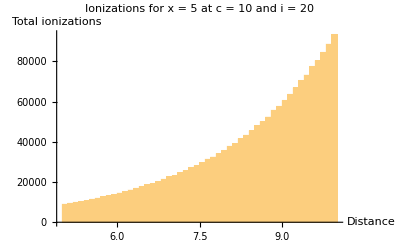

```mathematica
Histogram[l3[[2,1]],{10-5,10,0.1},AxesLabel->{"Distance", "Total ionizations"},PlotLabel->"Ionizations for x = 5 at c = 10 and i = 20"]
```

```mathematica
fig9=-Graphics-
```

-Graphics-

```mathematica
Export["/Users/wbowers/Documents/stem-fellowship/tif-figs/sample-space.TIFF",fig9,ImageResolution->600]
```

/Users/wbowers/Documents/stem-fellowship/tif-figs/sample-space.TIFF

#### Parallel plate breakdown 1D

```mathematica
FindBreakdown[r_,γ_,reps_] := Module[{alpha, idx,Nc, Ni},
alpha = FindAlpha[r,reps][[1]];
Nc = Log[γ]/alpha + r ;
Ni = (1/r)(Nc);
{Nc,Ni}]
```

```mathematica
bdpp1d = Table[FindBreakdown[r,50,500],{r,1/50,5,1/4}]
```

{{4.380.24,219.12.},{6.510.29,24.11.1},{9.030.11,17.370.21},{11.810.10,15.340.13},{15.190.09,14.900.09},{19.430.20,15.300.15},{24.90.4,16.380.29},{30.70.5,17.330.27},{38.60.7,19.10.4},{48.30.6,21.260.25},{59.60.8,23.670.30},{73.31.7,26.50.6},{84.83.5,28.11.1},{113.4.,34.61.3},{153.7.,43.42.0},{185.6.,49.11.5},{246.13.,61.33.2},{311.19.,73.4.},{406.38.,90.8.},{447.34.,94.7.}}

```mathematica
bdpp1d={{4.380.24,219.12.},{6.510.29,24.11.1},{9.030.11,17.370.21},{11.810.10,15.340.13},{15.190.09,14.900.09},{19.430.20,15.300.15},{24.90.4,16.380.29},{30.70.5,17.330.27},{38.60.7,19.10.4},{48.30.6,21.260.25},{59.60.8,23.670.30},{73.31.7,26.50.6},{84.83.5,28.11.1},{113.4.,34.61.3},{153.7.,43.42.0},{185.6.,49.11.5},{246.13.,61.33.2},{311.19.,73.4.},{406.38.,90.8.},{447.34.,94.7.}}
```

{{4.380.24,219.12.},{6.510.29,24.11.1},{9.030.11,17.370.21},{11.810.10,15.340.13},{15.190.09,14.900.09},{19.430.20,15.300.15},{24.90.4,16.380.29},{30.70.5,17.330.27},{38.60.7,19.10.4},{48.30.6,21.260.25},{59.60.8,23.670.30},{73.31.7,26.50.6},{84.83.5,28.11.1},{113.4.,34.61.3},{153.7.,43.42.0},{185.6.,49.11.5},{246.13.,61.33.2},{311.19.,73.4.},{406.38.,90.8.},{447.34.,94.7.}}

```mathematica
javabd1d={{Around[5.700231943597744,0.01207241166528697],Around[28.50115971798872,0.06036205832643485]},{Around[6.259659518165803,0.01294585426723786],Around[24.075613531406933,0.049791747181684075]},{Around[6.956648887715002,0.006510191038770662],Around[21.08075420519698,0.01972785163263837]},{Around[8.666186577739973,0.01778912290701574],Around[17.332373155479946,0.03557824581403148]},{Around[10.558215754398047,0.018609784723081196],Around[15.997296597572799,0.028196643519819993]},{Around[12.189849737655585,0.1691424999247856],Around[15.430189541336182,0.2141044302845387]},{Around[15.233034583855726,0.5468246433362867],Around[15.233034583855726,0.5468246433362867]},{Around[32.607032745474434,3.5391212217852397],Around[18.422052398573125,1.9995035151329037]},{Around[37.56666730405342,4.788665312298926],Around[19.56597255419449,2.494096516822358]}{Around[226.1883191276727,34.15818691413011],Around[61.13197814261424,9.231942409224354]},{Around[312.9949279966182,39.66595313492955],Around[78.24873199915454,9.916488283732388]}}
```

{{5.7000.012,28.500.06},{6.2600.013,24.080.05},{6.9570.007,21.0810.020},{8.6660.018,17.330.04},{10.5580.019,15.9970.028},{12.190.17,15.430.21},{15.20.5,15.20.5},{32.63.5,18.42.0},{8.51.710^3,1196.236.},{313.40.,78.10.}}

```mathematica
Solve[Log[51]==Ni*ProductLog[Nc/Ni *Exp[-Nc/Ni]],Ni]
```

{{Ni→(-Nc-Log[51])/Log[Log[51]/Nc]}}

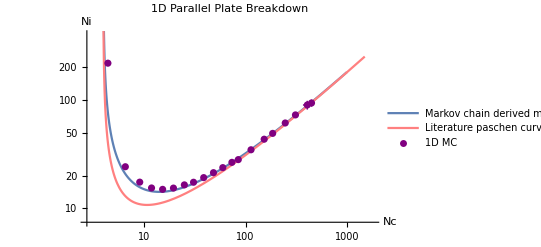

```mathematica
markovmodelfig=Show[LogLogPlot[(-Nc-Log[51])/Log[Log[51]/Nc],{Nc,3,1000},PlotLegends->{"Markov chain derived model"}],LogLogPlot[Nc/(Log[Nc]-Log[Log[51]]),{Nc,3,1500},PlotStyle->Pink,PlotLegends->{"Literature paschen curve"}],ListLogLogPlot[bdpp1d,PlotLegends->{"1D MC"},PlotStyle->Purple],AxesLabel->{"Nc","Ni"},PlotLabel->"1D Parallel Plate Breakdown",PlotRange->{{1,7.5},{2,6}},AxesOrigin->{1,2}]
```

```mathematica
Export["/Users/wbowers/Documents/stem-fellowship/figures/1d-pp-breakdown-wb-version.TIFF",markovmodelfig,ImageResolution->600]
```

/Users/wbowers/Documents/stem-fellowship/figures/1d-pp-breakdown-wb-version.TIFF

### Parallel plate breakdown 3D

```mathematica
FindBreakdown3D[d_,γ_,tbound_,Ni0_,reps_]:=Module[{region,list,i,errors,max,params,fit,error,p1,p2,p3,p4,f,vals,errorslist,listForFit},
list = Table[{Ni,AvgElectrons3D[d,Ni,d,15,tbound,reps] },{Ni,Ni0-3,Ni0+3}];
listForFit = {#[[1]],#[[2,1]]}&/@list;
errorslist = #[[2,2]]&/@list;
fit=NonlinearModelFit[listForFit,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/errorslist^2];
f=(Log[(γ-p3)/p1]/p2);
error={D[f,p1],D[f,p2],D[f,p3]}.fit["CovarianceMatrix"].Transpose[{D[f,p1],D[f,p2],D[f,p3]}]/.fit["BestFitParameters"];
Around[f,Sqrt[error]]/.fit["BestFitParameters"]
]
```

```mathematica
FindBreakdown3Dv2[4.5,50,0.8,30,3000]
```

{{27,45.50.7},{28,46.10.7},{29,47.50.7},{30,48.50.7},{31,48.70.8},{32,49.90.8},{33,51.30.8}}

32.010.21

```mathematica
left=Table[{d,FindBreakdown3Dv2[d,50,0.8,20,500]},{d,5,6,0.5}]
```

{{5.,21.20.4},{5.5,16.750.35},{6.,11.5.}}

```mathematica
min=Table[{d,FindBreakdown3Dv2[d,50,0.8,10,100]},{d,6,16.5,2}]
```

{{6,14.40.4},{8,11.730.13},{10,10.7900.034},{12,10.600.04},{14,10.520.07},{16,10.700.05}}

```mathematica
right2=Table[{d,FindBreakdown3Dv2[d,50,0.8,13,50]},{d,17,57,4}]
```

{{17,10.810.08},{21,11.240.04},{25,12.070.09},{29,12.660.05},{33,13.450.05},{37,14.2550.029},{41,14.9390.018},{45,15.660.09},{49,16.490.22},{53,17.480.09},{57,17.740.30}}

```mathematica
right3=Table[{d,FindBreakdown3Dv2[d,50,0.8,17,25]},{d,60,100,8}]
```

{{60,18.520.09},{68,19.970.07},{76,21.310.35},{84,23.71.2},{92,24.70.9},{100,26.21.4}}

```mathematica
bdfinal={{4.5,32.010.21},{5.,21.20.4},{5.5,16.750.35},{6,14.40.4},{8,11.730.13},{10,10.7900.034},{12,10.600.04},{14,10.520.07},{16,10.700.05},{17,10.770.06},{20,11.180.06},{23,11.640.07},{26,12.210.06},{32,13.270.05},{37,14.2550.029},{41,14.9390.018},{49,16.490.22},{60,18.520.09},{76,21.310.35},{92,24.70.9},{100,26.21.4}}
```

{{4.5,32.010.21},{5.,21.20.4},{5.5,16.750.35},{6,14.40.4},{8,11.730.13},{10,10.7900.034},{12,10.600.04},{14,10.520.07},{16,10.700.05},{17,10.770.06},{20,11.180.06},{23,11.640.07},{26,12.210.06},{32,13.270.05},{37,14.2550.029},{41,14.9390.018},{49,16.490.22},{60,18.520.09},{76,21.310.35},{92,24.70.9},{100,26.21.4}}

```mathematica
javabd3d={{Around[3.9349346617986107,0.004098654929587719],100},{7.,Around[12.5973499575545,0.021042290566655936]},{10.,Around[10.665900655226146,0.01147892717515875]},{20.,Around[11.199362729457336,0.0055071173430502485]},{40.,Around[14.831063909226039,0.011373607275817859]},{80.,Around[22.424620315119526,0.003938560064511855]},{160.,Around[36.60786133347448,0.009721595486457082]}}
```

{{3.9350.004,100},{7.,12.5970.021},{10.,10.6660.011},{20.,11.1990.006},{40.,14.8310.011},{80.,22.4250.004},{160.,36.6080.010}}

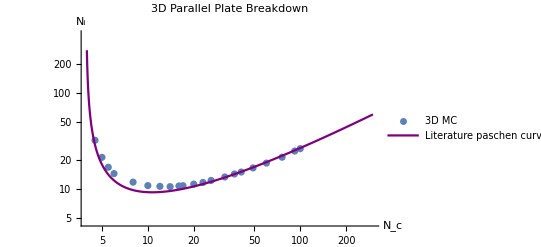

```mathematica
fig10=Show[ListLogLogPlot[bdfinal,PlotLegends->{"3D MC"}],LogLogPlot[0.86*Nc/(Log[Nc]-Log[Log[51]]),{Nc,3.9,300},PlotStyle->Purple,PlotLegends->{"Literature paschen curve"}],PlotRange->{1.5,6},AxesOrigin->{1,1.5},AxesLabel->{Subscript[N,c],Subscript[N,i]},PlotLabel->"3D Parallel Plate Breakdown"]
```

```mathematica
Export["/Users/wbowers/Documents/stem-fellowship/figures/3d-pp-breakdown-wb-version.TIFF",fig10,ImageResolution->600]
```

/Users/wbowers/Documents/stem-fellowship/figures/3d-pp-breakdown-wb-version.TIFF

#### Sphere-in-sphere breakdown

```mathematica
FindBreakdownSS[Nc_,γ_,Ni0_,dt_,reps_]:=Module[{region,list,i,errors,max,params,fit,error,p1,p2,p3,p4,f,vals,errorslist,listForFit},
list = Table[{Ni,AvgElectronsEuler[Nc,Ni,5,15,dt,4/5,False,reps]},{Ni,Ni0-3,Ni0+2}];
Print[list];
listForFit = {#[[1]],#[[2,1]]}&/@list;
errorslist = #[[2,2]]&/@list;
fit=NonlinearModelFit[listForFit,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/errorslist^2];
f=(Log[(γ-p3)/p1]/p2);
error={D[f,p1],D[f,p2],D[f,p3]}.fit["CovarianceMatrix"].Transpose[{D[f,p1],D[f,p2],D[f,p3]}]/.fit["BestFitParameters"];
Around[f,Sqrt[error]]/.fit["BestFitParameters"]
]
```

```mathematica
AvgElectronsEuler[10,5,5,15,1/5,4/5,True,500]
```

1000 * energy error error: 11.00186428

V/NC: 15/2

λ: 1/2

Geometry: SS

Collisions: 36.30.9

Mean path: 30.78891720263

5.440.15

```mathematica
FindNC[Ni_,γ_,Nc0_,dt_,reps_]:=Module[{region,list,i,errors,max,params,fit,error,p1,p2,p3,p4,f,vals,errorslist,listForFit},
list = Table[{Nc,AvgElectronsEuler[Nc,Ni,5,15,dt,4/5,False,reps]},{Nc,Nc0-1,Nc0+1,1/2}];
Print[list];
listForFit = {#[[1]],#[[2,1]]}&/@list;
errorslist = #[[2,2]]&/@list;
fit=NonlinearModelFit[listForFit,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/errorslist^2];
f=(Log[(γ-p3)/p1]/p2);
error={D[f,p1],D[f,p2],D[f,p3]}.fit["CovarianceMatrix"].Transpose[{D[f,p1],D[f,p2],D[f,p3]}]/.fit["BestFitParameters"];
Around[f,Sqrt[error]]/.fit["BestFitParameters"]
]
```

```mathematica
FindNC[100,50,4,1/5,300]
```

{{3,18.91.2},{7/2,34.41.9},{4,50.12.8},{9/2,77.4.},{5,130.7.}}

3.970.05

```mathematica
FindBreakdownSS[5,50,25,2/5,300]
```

{{22,47.02.2},{23,44.02.2},{24,45.92.5},{25,50.32.3},{26,53.82.6},{27,50.62.8},{28,58.93.2}}

25.60.8

```mathematica
FindBreakdownSS[7,50,15,2/5,50]
```

{{12,38.23.4},{13,45.4.},{14,53.6.},{15,58.6.},{16,81.8.},{17,73.9.},{18,93.8.}}

13.580.31

```mathematica
FindBreakdownSS[12,50,8,2/5,50]
```

{{5,4.920.18},{6,7.760.29},{7,12.60.5},{8,18.20.7},{9,25.81.2},{10,40.92.5}}

10.650.15

```mathematica
FindBreakdownSS[30,50,13,2/5,30]
```

{{10,16.91.1},{11,27.41.5},{12,43.02.8},{13,66.4.},{14,99.6.},{15,160.9.}}

12.360.04

```mathematica
FindBreakdownSS[50,50,15,2/5,20]
```

{{12,13.40.9},{13,21.91.6},{14,31.32.2},{15,59.4.},{16,87.5.},{17,129.11.}}

14.830.09

```mathematica
FindBreakdownSS[90,50,19,2/5,20]
```

{{16,13.41.4},{17,21.41.8},{18,36.92.3},{19,45.63.0},{20,71.5.},{21,110.8.}}

19.030.12

```mathematica
FindBreakdownSS[150,50,24,2/5,10]
```

{{21,14.82.5},{22,20.51.5},{23,23.5.},{24,37.5.},{25,42.7.},{26,81.11.}}

25.000.20

```mathematica
ssbd={{4.0360.018,100},{5,25.60.8},{7,13.580.31},{12,10.650.15},{30,12.360.04},{50,14.830.09},{90,19.030.12},{150,25.000.20}}
```

{{4.0360.018,100},{5,25.60.8},{7,13.580.31},{12,10.650.15},{30,12.360.04},{50,14.830.09},{90,19.030.12},{150,25.000.20}}

```mathematica
sophiedata = {{10.0,11.1},{20,11.3},{30,12.4}}
```

{{10.,11.1},{20,11.3},{30,12.4}}

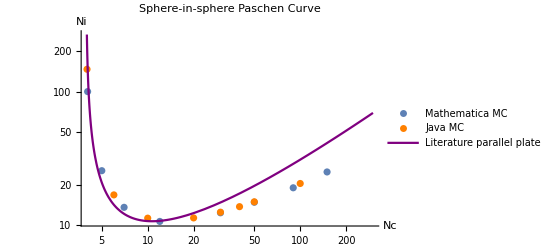

```mathematica
comparedata=Show[ListLogLogPlot[ssbd,PlotLegends->{"Mathematica MC"}],ListLogLogPlot[sophiessbd,PlotStyle->Orange,PlotLegends->{"Java MC"}],LogLogPlot[Nc/(Log[Nc]-Log[Log[51]]),{Nc,0,300},PlotStyle->Purple,PlotLegends->{"Literature parallel plate paschen curve"}],AxesLabel->{Nc,Ni},PlotLabel->"Sphere-in-sphere Paschen Curve",PlotRange->All]
```

```mathematica
Export["/Users/wbowers/Documents/stem-fellowship/figures/ss-breakdownf.TIFF",fig7,ImageResolution->600]
```

```mathematica
drwhitmerdata={{6.4940.019,15.},{5.4690.017,20.},{10,11.2270.008},{17.8,11.0260.009},{31.6,12.6360.006},{56.2,15.5580.020},{100.,20.3500.025}}
```

{{6.4940.019,15.},{5.4690.017,20.},{10,11.2270.008},{17.8,11.0260.009},{31.6,12.6360.006},{56.2,15.5580.020},{100.,20.3500.025}}

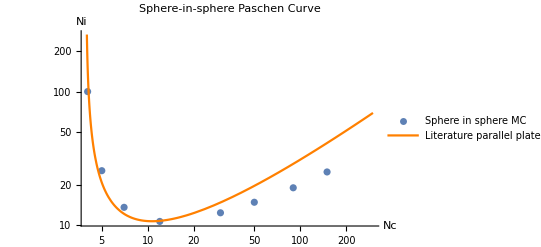

```mathematica
fig11=Show[ListLogLogPlot[ssbd,PlotLegends->{"Sphere in sphere MC"}],LogLogPlot[Nc/(Log[Nc]-Log[Log[51]]),{Nc,0,300},PlotStyle->Orange,PlotLegends->{"Literature parallel plate curve"}],AxesLabel->{Nc,Ni},PlotLabel->"Sphere-in-sphere Paschen Curve",PlotRange->All]
```

```mathematica
Export["/Users/wbowers/Documents/High-res-fusor-figures/ss-breakdown-wb-version.png",fig11,ImageResolution->300]
```

/Users/wbowers/Documents/High-res-fusor-figures/ss-breakdown-wb-version.png

#### Sphere-in-cylinder breakdown

```mathematica
FindBreakdownNISC[λ_,γ_,Ni0_,reps_]:=Module[{region,list,i,errors,max,params,fit,error,p1,p2,p3,p4,f,vals,errorslist,listForFit},
list = ParallelTable[{Ni,MaxElectrons[λ,Ni,reps]},{Ni,Ni0-3/2,Ni0+3/2,1/2}];
Print[list];
listForFit = {#[[1]],#[[2,1]]}&/@list;
errorslist = #[[2,2]]&/@list;
fit=NonlinearModelFit[listForFit,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/errorslist^2];
f=(Log[(γ-p3)/p1]/p2);
error={D[f,p1],D[f,p2],D[f,p3]}.fit["CovarianceMatrix"].Transpose[{D[f,p1],D[f,p2],D[f,p3]}]/.fit["BestFitParameters"];
Around[f,Sqrt[error]]/.fit["BestFitParameters"]
]
```

```mathematica
FindBreakdownNCSC[Ni_,γ_,Nc0_,reps_]:=Module[{region,list,i,errors,max,params,fit,error,p1,p2,p3,p4,f,vals,errorslist,listForFit},
list = ParallelTable[{Nc,MaxElectrons[53/(10*Nc),Ni,reps]},{Nc,Nc0-1,Nc0+1,1/2}];
Print[list];
listForFit = {#[[1]],#[[2,1]]}&/@list;
errorslist = #[[2,2]]&/@list;
fit=NonlinearModelFit[listForFit,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/errorslist^2];
f=(Log[(γ-p3)/p1]/p2);
error={D[f,p1],D[f,p2],D[f,p3]}.fit["CovarianceMatrix"].Transpose[{D[f,p1],D[f,p2],D[f,p3]}]/.fit["BestFitParameters"];
Around[f,Sqrt[error]]/.fit["BestFitParameters"]
]
```

```mathematica
FindBreakdownNCSC[40,50,34/10,500]
```

0.63622

0.645566

-0.746137

-0.756372

-0.665681

{{12/5,17.61.3},{29/10,31.32.1},{17/5,47.43.4},{39/10,83.6.},{22/5,101.7.}}

3.410.07

NC = 10

```mathematica
FindBreakdownNCSC[30,50,4,500]
```

0.659182

0.754227

-0.645615

0.691999

-0.708711

{{3,26.91.9},{7/2,41.92.7},{4,74.5.},{9/2,92.6.},{5,128.9.}}

3.630.07

```mathematica
FindBreakdownNCSC[18,50,4,500]
```

-0.858654

-0.599666

0.731309

-0.75725

-0.616007

{{3,17.81.4},{7/2,30.22.1},{4,31.02.1},{9/2,52.4.},{5,60.4.}}

4.620.18

```mathematica
FindBreakdownNISC[53/100,50,11.1,1000]
```

-1.

0.367845

-6.29888×10^-9

-1.

0.938665

0.22094

0.936544

{{9.6,35.13.1},{10.1,41.11.6},{10.6,43.81.2},{11.1,50.71.3},{11.6,58.22.3},{12.1,66.63.3},{12.6,99.10.}}

11.090.07

```mathematica
electronvals={{9.6,35.13.1},{10.1,41.11.6},{10.6,43.81.2},{11.1,50.71.3},{11.6,58.22.3},{12.1,66.63.3}}
listForFit = {#[[1]],#[[2,1]]}&/@electronvals;
errorslist = #[[2,2]]&/@electronvals;
fit=NonlinearModelFit[listForFit,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/errorslist^2];
f=(Log[(50-p3)/p1]/p2);
error={D[f,p1],D[f,p2],D[f,p3]}.fit["CovarianceMatrix"].Transpose[{D[f,p1],D[f,p2],D[f,p3]}]/.fit["BestFitParameters"];
res=Around[f,Sqrt[error]]/.fit["BestFitParameters"]
```

{{9.6,35.13.1},{10.1,41.11.6},{10.6,43.81.2},{11.1,50.71.3},{11.6,58.22.3},{12.1,66.63.3}}

11.070.04

```mathematica
res[[1]]
```

11.0654

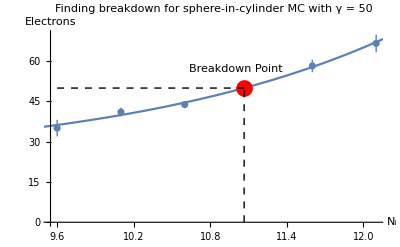

```mathematica
fig7=Show[ListPlot[electronvals],Plot[fit[x],{x,9,16}],Graphics[{Red,PointSize[0.03],Point[{res[[1]],50}]}],Graphics[{Dashed,Black,Line[{{9.6,50},{res[[1]],50}}],Line[{{res[[1]],0},{res[[1]],50}}]}],Graphics[Text["Breakdown Point",{11,57}]],AxesLabel->{Subscript["N","i"],"Electrons"},PlotLabel->"Finding breakdown for sphere-in-cylinder MC with γ = 50"]
```

```mathematica
Export["/Users/wbowers/Documents/stem-fellowship/figures/scanning-ni.TIFF",fig7,ImageResolution->600]
```

/Users/wbowers/Documents/stem-fellowship/figures/scanning-ni.TIFF

```mathematica
FindBreakdownNISC[53/178,50,11.1,500]
```

-4.36402×10^-9

-1.28008×10^-8

-1.

-7.82048×10^-9

2.20918×10^-33

General::munfl: (2.20918×10^-33)^10 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.

-1.30523×10^-8

{{9.6,26.80.8},{10.1,34.91.1},{10.6,42.11.4},{11.1,55.6.},{11.6,75.8.},{12.1,73.22.9},{12.6,95.4.}}

10.990.07

```mathematica
FindBreakdownNISC[53/200,50,13,100]
```

$Aborted

-0.934342

-5.14173×10^-9

-1.

1.

0.

-0.912496

-1.

{{23/2,55.5.},{12,65.11.},{25/2,101.9.},{13,103.12.},{27/2,154.28.},{14,183.67.},{29/2,180.15.}}

11.380.14

```mathematica
FindBreakdownNISC[53/400,50,13,200]
```

-1.

-4.96763×10^-9

1.

-0.26817

-4.1359×10^-24

-6.18105×10^-9

1.

{{23/2,18.72.6},{12,23.50.8},{25/2,29.41.3},{13,38.42.0},{27/2,46.5.},{14,59.7.},{29/2,69.03.2}}

13.6800.029

```mathematica
FindBreakdownNISC[53/700,50,17,100]
```

0.589819

-1.

0.514641

0.214126

-0.907422

-0.913193

1.

{{31/2,28.92.3},{16,30.62.2},{33/2,45.12.},{17,46.4.},{35/2,60.92.8},{18,72.14.},{37/2,96.7.}}

17.120.06

```mathematica
FindBreakdownNISC[53/1100,50,23,100]
```

-1.

-0.970182

-0.306198

-0.918607

-0.265945

-1.03398×10^-25

-4.71216×10^-9

{{43/2,56.15.},{22,60.4.},{45/2,87.7.},{23,100.6.},{47/2,124.11.},{24,163.9.},{49/2,214.16.}}

21.530.19

```mathematica
FindBreakdownNISC[53/1500,50,24,80]
```

2.06795×10^-25

-6.58048×10^-9

-0.8947

0.305773

-0.355367

-0.882098

0.488683

{{45/2,24.32.9},{23,35.4.},{47/2,32.83.2},{24,41.13.1},{49/2,48.5.},{25,54.5.},{51/2,61.7.}}

24.710.12

```mathematica
scbreakdown={{5.3/3.410.07,40},{5.3/3.630.07,30},{5.3/4.620.18,18},{53/100,11.090.07},{53/200,11.380.14},{53/400,13.6800.029},{53/700,17.120.06},{53/1100,21.530.19},{53/1500,24.710.12}}
sbreakdownscaled={1/#[[1]],15*#[[2]]}&/@scbreakdown
```

{{1.5570.031,40},{1.4590.028,30},{1.150.04,18},{53/100,11.090.07},{53/200,11.380.14},{53/400,13.6800.029},{53/700,17.120.06},{53/1100,21.530.19},{53/1500,24.710.12}}

{{0.6420.013,600},{0.6850.013,450},{0.8720.034,270},{100/53,166.41.0},{200/53,170.62.2},{400/53,205.20.4},{700/53,256.81.0},{1100/53,322.92.8},{1500/53,370.71.7}}

```mathematica
sbreakdownscaled//N
```

{{0.6420.013,600.},{0.6850.013,450.},{0.8720.034,270.},{1.88679,166.41.0},{3.77358,170.62.2},{7.54717,205.20.4},{13.2075,256.81.0},{20.7547,322.92.8},{28.3019,370.71.7}}

```mathematica
ssbreakdownscaled={#[[1]]/5.3,15*#[[2]]}&/@ssbd
```

{{0.76160.0035,1500},{0.943396,383.11.},{1.32075,204.5.},{2.26415,159.82.2},{5.66038,185.40.5},{9.43396,222.41.4},{16.9811,285.41.8},{28.3019,375.03.1}}

```mathematica
sophiessbreakdownscaled={#[[1]]/5.3,15*#[[2]]}&/@sophiessbd
```

{{0.754717,2205.29.},{1.13208,252.9.},{1.88679,169.00.8},{3.77358,169.70.4},{5.66038,187.420.20},{7.54717,206.120.19},{9.43396,224.140.23},{18.8679,307.370.24}}

```mathematica
sophiessbreakdownscaled={{0.7547169811320755,2205.29.},{1.1320754716981134,252.9.},{1.8867924528301887,169.00.8},{5.660377358490567,187.420.20},{18.867924528301888,307.370.24}}
```

{{0.754717,2205.29.},{1.13208,252.9.},{1.88679,169.00.8},{5.66038,187.420.20},{18.8679,307.370.24}}

```mathematica
combinedssbreakdown={{0.7547169811320755,2205.29.},{0.76160.0035,1500},{0.9433962264150944,383.11.},{1.1320754716981134,252.9.},{1.3207547169811322,204.5.},{1.8867924528301887,169.00.8},{2.264150943396227,159.82.2},{5.660377358490567,185.40.5},{9.433962264150944,222.41.4},{16.9811320754717,285.41.8},{18.867924528301888,307.370.24},{28.301886792452834,375.03.1}}
```

{{0.754717,2205.29.},{0.76160.0035,1500},{0.943396,383.11.},{1.13208,252.9.},{1.32075,204.5.},{1.88679,169.00.8},{2.26415,159.82.2},{5.66038,185.40.5},{9.43396,222.41.4},{16.9811,285.41.8},{18.8679,307.370.24},{28.3019,375.03.1}}

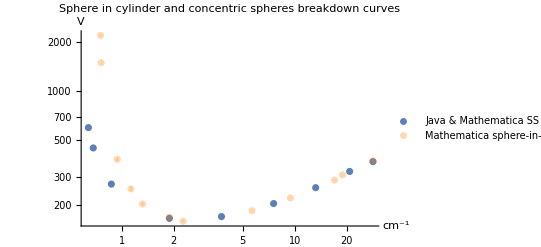

```mathematica
fig12=Show[ListLogLogPlot[sbreakdownscaled,PlotLegends->{"Java & Mathematica SS breakdown"}],ListLogLogPlot[combinedssbreakdown,PlotStyle->{Orange,Opacity[0.3]},PlotLegends->{"Mathematica sphere-in-sphere MC"}],PlotRange->All,PlotLabel->"Sphere in cylinder and concentric spheres breakdown curves",AxesLabel->{Superscript["cm","-1"],"V"}]
```

```mathematica
Export["/Users/wbowers/Documents/stem-fellowship/figures/ss-and-sc-breakdown.TIFF",fig12,ImageResolution->600]
```

/Users/wbowers/Documents/stem-fellowship/figures/ss-and-sc-breakdown.TIFF

#### Plotting fusor data

```mathematica
data=Drop[Import["/Users/wbowers/Downloads/RAWpashendata.txt","Table"],1]
```

{{17.4373,2086.77},{17.4627,2052.92},{17.4878,2069.5},{17.5153,2036.34},{17.549,2081.93},{17.5836,2041.17},{17.6141,2037.03},{17.641,2048.08},{17.6684,2031.5},{17.7051,2051.54},{17.7484,1998.34},{17.7916,2043.25},{17.8291,2030.12},{17.8664,1991.44},{17.9028,1962.42},{17.9676,1967.26},7141,{16656.5,2019.76},{16660,2057.06},{16660,2035.65},{16660,2054.99},{16660,2073.64},{16660,2073.64},{16660,2073.64},{16663.4,2073.64},{16666.9,2081.24},{16670.7,2081.24},{16677.3,2079.17},{16684,2102.66},{16690.9,2073.64},{16697.9,2077.79},{16704.9,2082.62},{----------,--------}}
 |  |  |  |

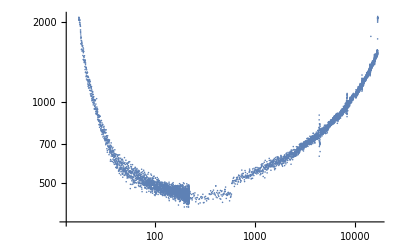

```mathematica
ListLogLogPlot[data]
```

```mathematica
b = 365
```

365

```mathematica
a = 15
```

15

```mathematica
k = Log[a / Log[1+1/(0.01)]]
```

1.17871

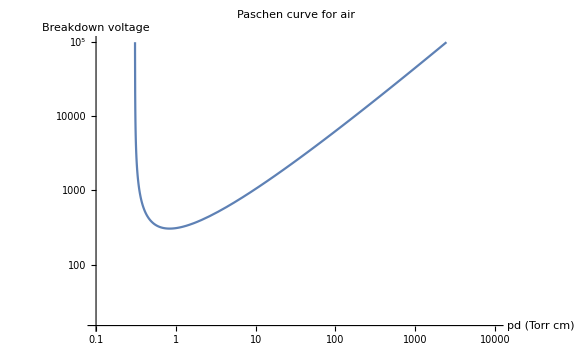

```mathematica
fig1=LogLogPlot[b x/(Log[x]+k),{x,0.1,10000},PlotRange->{{0.1,10000},{15,100000}},AxesOrigin->{0.1,15},PlotLabel->"Paschen curve for air",AxesLabel->{"pd (Torr cm)" , "Breakdown voltage"}]
```

```mathematica
Export["/Users/wbowers/Documents/stem-fellowship/tif-figs/air-paschen-curve.TIFF",fig1,ImageResolution->600]
```

/Users/wbowers/Documents/stem-fellowship/tif-figs/air-paschen-curve.TIFF

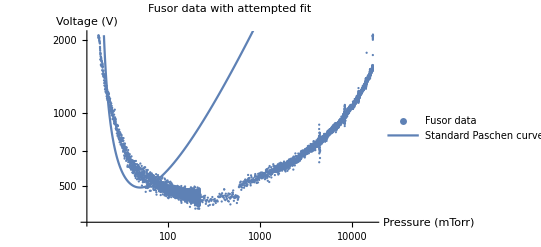

```mathematica
fig2=Show[ListLogLogPlot[data,PlotLegends->{"Fusor data"},PlotStyle->{PointSize[0.004]}],LogLogPlot[10x/(Log[x]-2.9),{x,20,1000},PlotLegends->{"Standard Paschen curve"}],AxesLabel->{"Pressure (mTorr)","Voltage (V)"},PlotLabel->"Fusor data with attempted fit"]
```

```mathematica
Export["/Users/wbowers/Documents/stem-fellowship/tif-figs/attempted-fit.TIFF",fig2,ImageResolution->600]
```

/Users/wbowers/Documents/stem-fellowship/tif-figs/attempted-fit.TIFF